# AdinkraTutorial.nb

```mathematica
$RecursionLimit=Infinity
```

∞

## Import Adinkra.wl

```mathematica
<<Adinkra.wl
```

```mathematica
BuildDate[Adinkra]
```

181130

### Function Lists

```mathematica
FunctionList[SpaceTime]
```

IndexRange[SpaceTime][Index], Index = mu, a, or RaiseCode

coordinates, Ϛ[mu], η[mu,nu], Cmetric[[a,b]], InverseCmetric[[a,b]], UD[Field,Ϛ[mu]] , Lap[Field], UP, DOWN, RaiseSTIndex[Field,RaiseCode1,RaiseCode2,...,RaiseCoden], RaiseFermionIndex[Field]

****************************************************************************************
****************************************************************************************

```mathematica
FunctionList[GenerateLandR]
```

NColors[D,Phi,Psi], LTable[DColor,Phi,Psi], RTable[DColor,Phi,Psi],GenerateLandR[DColor,Phi,Psi,Rep]

****************************************************************************************
****************************************************************************************

```mathematica
FunctionList[AdinkraEssentials]
```

IndexRange[AdinkraEssentials][Index], Index = p1, II, ReportLevel, or pm

***IMPORTANT****: Default Settings are VScaleFactor = VtildeScaleFactor = -I, VsoNScaleFactor = -I/(2 VsoNScaleFactor), VtildesoNScaleFactor = -I/(2 VtildesoNScaleFactor)

Reports: AdinkraReport[Rep,ReportLevel], AdinkraPreliminaryReport[L,R], AdinkraPreliminaryReport[Rep], AdinkraPreliminaryReportO[Rep], AdinkraHoloMonoReport[Rep], AdinkraSummaryReport[Rep], AdinkraFullReport[Rep]

Basic Functions: nMatrices[Matrices], nRows[Matrices], nColumns[Matrices], Commute[Matrix1,Matrix2], NColors[Rep], NColors[L,R], dmin[N], dbosons[Rep], dbosons[L,R], dfermions[Rep], dfermions[L,R], WordW[{p1,p2,...,pN}]

Intense Calculations: Gadget[Rep1,Rep2], BosonGadget[Rep1,Rep2], ListOfIdenticalMonoOrHolo[MonoOrHolo,Rep], NumDistinctHoloOrMono[HoloOrMono,Rep]

Print Functions: PrintL[Rep][II], PrintR[Rep][II], PrintGALR[Rep][II,JJ], PrintGARL[Rep][II,JJ], PrintV[Rep][II,JJ], PrintVtilde[Rep][II,JJ], PrintZetaGen[Rep][II], PrintHoloraumy[Rep][{p1,p2,...,pN}], PrintMonodromy[Rep][{p1,p2,...,pN}],PrintZetatildeGen[Rep][II], PrintHoloraumytilde[Rep][{p1,p2,...,pN}], PrintMonodromytilde[Rep][{p1,p2,...,pN}], PrintVtildePM[pm][Rep][II,JJ], PrintVtildePM[pm][Rep][II,JJ], PrintAllL[Rep], PrintAllR[Rep], PrintAllGALR[Rep], PrintAllGARL[Rep], PrintAllV[Rep], PrintAllVtilde[Rep], PrintAllZetaGen[Rep], PrintAllHoloraumy[Rep], PrintAllMonodromy[Rep],PrintAllZetatildeGen[Rep], PrintAllHoloraumytilde[Rep], PrintAllMonodromytilde[Rep], PrintAllVtildePM[pm][Rep], PrintAllVtildePM[pm][Rep], ,PrintSigmaProduct[Matrix], PrintLSigmaProduct[Rep], PrintRSigmaProduct[Rep]

Test Functions: CorrectDimensions[Rep], CorrectDimensions[L,R], TransposeTest[Rep], TransposeTest[L,R], InverseTest[Rep], InverseTest[L,R], RO[Rep], Chi0Report[L,R], GATest[Rep], GATest[L,R], soNTest[Matrices], su2Test[MgenPM[pm]][Rep], MutuallyCommuteTest[M1,M2], LinearlyIndependent[Mgen]

Data generated by GenerateAdinkraData[Rep], GenerateAdinkraData[Rep,Orthogonal], GenerateAdinkraDataO[Rep], GenerateAdinkraData[Rep,L], or GenerateAdinkraData[Rep,L,R]:
L[Rep], R[Rep], GALR[Rep], GARL[Rep], chi0[Rep], ncis[Rep], ntrans[Rep], V[Rep], Vtilde[Rep], VsoN[Rep], VtildesoN[Rep], ZetaGen[Rep], Holoraumy[Rep], Monodromy[Rep], ZetatildeGen[Rep], Holoraumytilde[Rep], Monodromytilde[Rep], VPM[pm][Rep], VtildePM[pm][Rep], VsoNPM[pm][Rep], VtildesoNPM[pm][Rep] cSoln[V[Rep]], cSoln[Vtilde[Rep]]

****************************************************************************************
****************************************************************************************

```mathematica
FunctionList[BasisDecomposition]
```

IndexRange[BasisDecomposition][Index], Index = mu, ahat, a, d, or n

General Matrix Tools:
sigma[mu], αmatrix[ahat], βmatrix[ahat], SigmaProduct[mu1,mu2,...,mun], SigmaProductMF[mu1,mu2,...,mun], SigmaMatrixProduct[mu,AnyMatrix], ρmatrix[mu,nu], ωmatrix[n][a], Basis[d][a,mu,nu], TestOrthogonalσ, TestρOrthogonal, TestωOrthogonal[n], TestBasisOrthogonal[d], Coeffs[d][Matrix][a,mu,nu]

GenerateCoeffs[Rep] generates adinkra representation specific functions:
LCoeffs[Rep][II], CheckLCoeffs[Rep], RCoeffs[Rep][II], CheckRCoeffs[Rep], VCoeffs[Rep][II,JJ], CheckVCoeffs[Rep], VtildeCoeffs[Rep][II,JJ], CheckVtildeCoeffs[Rep], VPMCoeffs[pm][Rep][II,JJ], CheckVPMCoeffs[pm][Rep], VtildePMCoeffs[pm][Rep][II,JJ], CheckVtildePMCoeffs[pm][Rep], NumberNonZero[LCoeffsMat], CoeffsSummaryReport[Rep], CoeffsFullReport[Rep_]

Print Functions:
 PrintSigmaProduct[Matrix], PrintBasis[Matrix], PrintLBasis[Rep][II], PrintRBasis[Rep][II], PrintGALRBasis[Rep][II,JJ], PrintGARLBasis[Rep][II,JJ], PrintVBasis[Rep][II,JJ], PrintVtildeBasis[Rep][II,JJ], PrintVPMBasis[pm][Rep][II,JJ], PrintVtildePMBasis[pm][Rep][II,JJ], PrintLSigmaProduct[Rep], PrintRSigmaProduct[Rep]

****************************************************************************************
****************************************************************************************

```mathematica
FunctionList[BC4Tools]
```

IndexRange[BC4Tools][Index], Index = n, a, μ, A, II, or tt

Functions: 
HPerm[a], H[[a]], S3Perm[μ], S3[[μ]], VierPerm[A], Vier[[A]], BC4[[n,a,μ,A,II,JJ]] , BC4Perm[n,a,μ,A][[II,JJ]], QuaternionTestIJK[Quat], QuaternionTestKJI[Quat], Digit[Num,Pow], ell[Rep][tt,a][II,JJ], kappa[Rep][ti,a][II,JJ], IellABColor[Rep][[a]], PrintIell[Rep][[a]], IellABCode[Rep][[a]], AntisymmetryCheck[Object1], BC4Color[n,a,μ,A][L], BC4ColorPerm[n,a,μ,A][L],BC4Boson[n,a,μ,A][L],BC4BosonPerm[n,a,μ,A][L], HList,S3List,VierList,PrintBC4Perm[n,a,μ,A],PrintBC4BosonPerm[n,a,μ,A],PrintBC4FermionPerm[n,a,μ,A],PrintBC4ColorPerm[n,a,μ,A],L[Q],L[Qtilde],L[RepCode]

****************************************************************************************
****************************************************************************************

```mathematica
FunctionList[GraphingTools]
```

IndexRange[GraphingTools][list]

 AdinkraGreen, AdinkraViolet, AdinkraOrange, AdinkraRed, padLmatrix[L], adjacencyToEdge[mat,col], buildrules[list], Valise, GraphAdinkra[L], GraphAdinkra[L,BuildRules[list], ExportAdinkra[L,BuildRules[list],filename]

****************************************************************************************
****************************************************************************************

```mathematica
FunctionList[Adinkra]
```

SpaceTime:
IndexRange[SpaceTime][Index], Index = mu, a, or RaiseCode

coordinates, Ϛ[mu], η[mu,nu], Cmetric[[a,b]], InverseCmetric[[a,b]], UD[Field,Ϛ[mu]] , Lap[Field], UP, DOWN, RaiseSTIndex[Field,RaiseCode1,RaiseCode2,...,RaiseCoden], RaiseFermionIndex[Field]

****************************************************************************************
****************************************************************************************

GenerateLandR:
NColors[D,Phi,Psi], LTable[DColor,Phi,Psi], RTable[DColor,Phi,Psi],GenerateLandR[DColor,Phi,Psi,Rep]

****************************************************************************************
****************************************************************************************

AdinkraEssentials:
IndexRange[AdinkraEssentials][Index], Index = p1, II, ReportLevel, or pm

***IMPORTANT****: Default Settings are VScaleFactor = VtildeScaleFactor = -I, VsoNScaleFactor = -I/(2 VsoNScaleFactor), VtildesoNScaleFactor = -I/(2 VtildesoNScaleFactor)

Reports: AdinkraReport[Rep,ReportLevel], AdinkraPreliminaryReport[L,R], AdinkraPreliminaryReport[Rep], AdinkraPreliminaryReportO[Rep], AdinkraHoloMonoReport[Rep], AdinkraSummaryReport[Rep], AdinkraFullReport[Rep]

Basic Functions: nMatrices[Matrices], nRows[Matrices], nColumns[Matrices], Commute[Matrix1,Matrix2], NColors[Rep], NColors[L,R], dmin[N], dbosons[Rep], dbosons[L,R], dfermions[Rep], dfermions[L,R], WordW[{p1,p2,...,pN}]

Intense Calculations: Gadget[Rep1,Rep2], BosonGadget[Rep1,Rep2], ListOfIdenticalMonoOrHolo[MonoOrHolo,Rep], NumDistinctHoloOrMono[HoloOrMono,Rep]

Print Functions: PrintL[Rep][II], PrintR[Rep][II], PrintGALR[Rep][II,JJ], PrintGARL[Rep][II,JJ], PrintV[Rep][II,JJ], PrintVtilde[Rep][II,JJ], PrintZetaGen[Rep][II], PrintHoloraumy[Rep][{p1,p2,...,pN}], PrintMonodromy[Rep][{p1,p2,...,pN}],PrintZetatildeGen[Rep][II], PrintHoloraumytilde[Rep][{p1,p2,...,pN}], PrintMonodromytilde[Rep][{p1,p2,...,pN}], PrintVtildePM[pm][Rep][II,JJ], PrintVtildePM[pm][Rep][II,JJ], PrintAllL[Rep], PrintAllR[Rep], PrintAllGALR[Rep], PrintAllGARL[Rep], PrintAllV[Rep], PrintAllVtilde[Rep], PrintAllZetaGen[Rep], PrintAllHoloraumy[Rep], PrintAllMonodromy[Rep],PrintAllZetatildeGen[Rep], PrintAllHoloraumytilde[Rep], PrintAllMonodromytilde[Rep], PrintAllVtildePM[pm][Rep], PrintAllVtildePM[pm][Rep], ,PrintSigmaProduct[Matrix], PrintLSigmaProduct[Rep], PrintRSigmaProduct[Rep]

Test Functions: CorrectDimensions[Rep], CorrectDimensions[L,R], TransposeTest[Rep], TransposeTest[L,R], InverseTest[Rep], InverseTest[L,R], RO[Rep], Chi0Report[L,R], GATest[Rep], GATest[L,R], soNTest[Matrices], su2Test[MgenPM[pm]][Rep], MutuallyCommuteTest[M1,M2], LinearlyIndependent[Mgen]

Data generated by GenerateAdinkraData[Rep], GenerateAdinkraData[Rep,Orthogonal], GenerateAdinkraDataO[Rep], GenerateAdinkraData[Rep,L], or GenerateAdinkraData[Rep,L,R]:
L[Rep], R[Rep], GALR[Rep], GARL[Rep], chi0[Rep], ncis[Rep], ntrans[Rep], V[Rep], Vtilde[Rep], VsoN[Rep], VtildesoN[Rep], ZetaGen[Rep], Holoraumy[Rep], Monodromy[Rep], ZetatildeGen[Rep], Holoraumytilde[Rep], Monodromytilde[Rep], VPM[pm][Rep], VtildePM[pm][Rep], VsoNPM[pm][Rep], VtildesoNPM[pm][Rep] cSoln[V[Rep]], cSoln[Vtilde[Rep]]

****************************************************************************************
****************************************************************************************

BasisDecomposition:
IndexRange[BasisDecomposition][Index], Index = mu, ahat, a, d, or n

General Matrix Tools:
sigma[mu], αmatrix[ahat], βmatrix[ahat], SigmaProduct[mu1,mu2,...,mun], SigmaProductMF[mu1,mu2,...,mun], SigmaMatrixProduct[mu,AnyMatrix], ρmatrix[mu,nu], ωmatrix[n][a], Basis[d][a,mu,nu], TestOrthogonalσ, TestρOrthogonal, TestωOrthogonal[n], TestBasisOrthogonal[d], Coeffs[d][Matrix][a,mu,nu]

GenerateCoeffs[Rep] generates adinkra representation specific functions:
LCoeffs[Rep][II], CheckLCoeffs[Rep], RCoeffs[Rep][II], CheckRCoeffs[Rep], VCoeffs[Rep][II,JJ], CheckVCoeffs[Rep], VtildeCoeffs[Rep][II,JJ], CheckVtildeCoeffs[Rep], VPMCoeffs[pm][Rep][II,JJ], CheckVPMCoeffs[pm][Rep], VtildePMCoeffs[pm][Rep][II,JJ], CheckVtildePMCoeffs[pm][Rep], NumberNonZero[LCoeffsMat], CoeffsSummaryReport[Rep], CoeffsFullReport[Rep_]

Print Functions:
 PrintSigmaProduct[Matrix], PrintBasis[Matrix], PrintLBasis[Rep][II], PrintRBasis[Rep][II], PrintGALRBasis[Rep][II,JJ], PrintGARLBasis[Rep][II,JJ], PrintVBasis[Rep][II,JJ], PrintVtildeBasis[Rep][II,JJ], PrintVPMBasis[pm][Rep][II,JJ], PrintVtildePMBasis[pm][Rep][II,JJ], PrintLSigmaProduct[Rep], PrintRSigmaProduct[Rep]

****************************************************************************************
****************************************************************************************

BC4Tools:

IndexRange[BC4Tools][Index], Index = n, a, μ, A, II, or tt

Functions: 
HPerm[a], H[[a]], S3Perm[μ], S3[[μ]], VierPerm[A], Vier[[A]], BC4[[n,a,μ,A,II,JJ]] , BC4Perm[n,a,μ,A][[II,JJ]], QuaternionTestIJK[Quat], QuaternionTestKJI[Quat], Digit[Num,Pow], ell[Rep][tt,a][II,JJ], kappa[Rep][ti,a][II,JJ], IellABColor[Rep][[a]], PrintIell[Rep][[a]], IellABCode[Rep][[a]], AntisymmetryCheck[Object1], BC4Color[n,a,μ,A][L], BC4ColorPerm[n,a,μ,A][L],BC4Boson[n,a,μ,A][L],BC4BosonPerm[n,a,μ,A][L], HList,S3List,VierList,PrintBC4Perm[n,a,μ,A],PrintBC4BosonPerm[n,a,μ,A],PrintBC4FermionPerm[n,a,μ,A],PrintBC4ColorPerm[n,a,μ,A],L[Q],L[Qtilde],L[RepCode]

****************************************************************************************
****************************************************************************************

GraphingTools:
IndexRange[GraphingTools][list]

 AdinkraGreen, AdinkraViolet, AdinkraOrange, AdinkraRed, padLmatrix[L], adjacencyToEdge[mat,col], buildrules[list], Valise, GraphAdinkra[L], GraphAdinkra[L,BuildRules[list], ExportAdinkra[L,BuildRules[list],filename]

****************************************************************************************
****************************************************************************************

### Introduction to some of these functions

#### Within FunctionList[SpaceTime]

```mathematica
η[1,1]
```

1

```mathematica
Cmetric
```

{{0,-1,0,0},{1,0,0,0},{0,0,0,1},{0,0,-1,0}}

```mathematica
Lap[SomeField[t,x,y,z]]
```

SomeField^(0,0,0,2)[t,x,y,z]+SomeField^(0,0,2,0)[t,x,y,z]+SomeField^(0,2,0,0)[t,x,y,z]-SomeField^(2,0,0,0)[t,x,y,z]

```mathematica
Lap[A[2][t,x,y,z]]
```

A[2]^(0,0,0,2)[t,x,y,z]+A[2]^(0,0,2,0)[t,x,y,z]+A[2]^(0,2,0,0)[t,x,y,z]-A[2]^(2,0,0,0)[t,x,y,z]

#### Within FunctionList[AdinkraEssentials]

```mathematica
IndexRange[AdinkraEssentials][ReportLevel]
```

1, 2, 3, 4, 5, 6, 7, 8

```mathematica
FunctionList[AdinkraEssentials]
```

IndexRange[AdinkraEssentials][Index], Index = p1, II, ReportLevel, or pm

***IMPORTANT****: Default Settings are VScaleFactor = VtildeScaleFactor = -I, VsoNScaleFactor = -I/(2 VsoNScaleFactor), VtildesoNScaleFactor = -I/(2 VtildesoNScaleFactor)

Reports: AdinkraReport[Rep,ReportLevel], AdinkraPreliminaryReport[L,R], AdinkraPreliminaryReport[Rep], AdinkraPreliminaryReportO[Rep], AdinkraHoloMonoReport[Rep], AdinkraSummaryReport[Rep], AdinkraFullReport[Rep]

Basic Functions: nMatrices[Matrices], nRows[Matrices], nColumns[Matrices], Commute[Matrix1,Matrix2], NColors[Rep], NColors[L,R], dmin[N], dbosons[Rep], dbosons[L,R], dfermions[Rep], dfermions[L,R], WordW[{p1,p2,...,pN}]

Intense Calculations: Gadget[Rep1,Rep2], BosonGadget[Rep1,Rep2], ListOfIdenticalMonoOrHolo[MonoOrHolo,Rep], NumDistinctHoloOrMono[HoloOrMono,Rep]

Print Functions: PrintL[Rep][II], PrintR[Rep][II], PrintGALR[Rep][II,JJ], PrintGARL[Rep][II,JJ], PrintV[Rep][II,JJ], PrintVtilde[Rep][II,JJ], PrintZetaGen[Rep][II], PrintHoloraumy[Rep][{p1,p2,...,pN}], PrintMonodromy[Rep][{p1,p2,...,pN}],PrintZetatildeGen[Rep][II], PrintHoloraumytilde[Rep][{p1,p2,...,pN}], PrintMonodromytilde[Rep][{p1,p2,...,pN}], PrintVtildePM[pm][Rep][II,JJ], PrintVtildePM[pm][Rep][II,JJ], PrintAllL[Rep], PrintAllR[Rep], PrintAllGALR[Rep], PrintAllGARL[Rep], PrintAllV[Rep], PrintAllVtilde[Rep], PrintAllZetaGen[Rep], PrintAllHoloraumy[Rep], PrintAllMonodromy[Rep],PrintAllZetatildeGen[Rep], PrintAllHoloraumytilde[Rep], PrintAllMonodromytilde[Rep], PrintAllVtildePM[pm][Rep], PrintAllVtildePM[pm][Rep], ,PrintSigmaProduct[Matrix], PrintLSigmaProduct[Rep], PrintRSigmaProduct[Rep]

Test Functions: CorrectDimensions[Rep], CorrectDimensions[L,R], TransposeTest[Rep], TransposeTest[L,R], InverseTest[Rep], InverseTest[L,R], RO[Rep], Chi0Report[L,R], GATest[Rep], GATest[L,R], soNTest[Matrices], su2Test[MgenPM[pm]][Rep], MutuallyCommuteTest[M1,M2], LinearlyIndependent[Mgen]

Data generated by GenerateAdinkraData[Rep], GenerateAdinkraData[Rep,Orthogonal], GenerateAdinkraDataO[Rep], GenerateAdinkraData[Rep,L], or GenerateAdinkraData[Rep,L,R]:
L[Rep], R[Rep], GALR[Rep], GARL[Rep], chi0[Rep], ncis[Rep], ntrans[Rep], V[Rep], Vtilde[Rep], VsoN[Rep], VtildesoN[Rep], ZetaGen[Rep], Holoraumy[Rep], Monodromy[Rep], ZetatildeGen[Rep], Holoraumytilde[Rep], Monodromytilde[Rep], VPM[pm][Rep], VtildePM[pm][Rep], VsoNPM[pm][Rep], VtildesoNPM[pm][Rep] cSoln[V[Rep]], cSoln[Vtilde[Rep]]

****************************************************************************************
****************************************************************************************

## N=4, Various Representations

### ONshellCM, and a non-adinkraic representation to test catches

```mathematica
L[OnShellCM] ={({{1, 0, 0, 0}, {0, 0, 0, -1}}),({{0, 1, 0, 0}, {0, 0, 1, 0}}),({{0, 0, 1, 0}, {0, -1, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 0, 0}})}
```

{{{1,0,0,0},{0,0,0,-1}},{{0,1,0,0},{0,0,1,0}},{{0,0,1,0},{0,-1,0,0}},{{0,0,0,1},{1,0,0,0}}}

```mathematica
R[OnShellCM] = Table[Transpose[L[OnShellCM][[Ii]]],{Ii,1,4}]
```

{{{1,0},{0,0},{0,0},{0,-1}},{{0,0},{1,0},{0,1},{0,0}},{{0,0},{0,-1},{1,0},{0,0}},{{0,1},{0,0},{0,0},{1,0}}}

```mathematica
L[ID] = L[OnShellCM];
R[ID] = L[Q];
```

```mathematica
GenerateAdinkraData[OnShellCM]
```

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], L, R, GALR, GARL, V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = OnShellCM

```mathematica
GenerateCoeffs[OnShellCM]
```

{GARLCoeffs, VtildeCoeffs, and VtildePMCoeffs are loaded for Rep = OnShellCM}

```mathematica
PrintAllGARL[OnShellCM]
```

{(2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 2),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 0),(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 2)}

```mathematica
PrintGARLBasis[OnShellCM][1,1]
```

I_4+α_1 β_1

```mathematica
PrintGARLBasis[OnShellCM][3,3]
```

I_4-α_1 β_1

```mathematica
PrintAllVtilde[OnShellCM]
```

{(0 | -ⅈ/2 | 0 | 0
ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2
0 | 0 | ⅈ/2 | 0),(0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | ⅈ/2
ⅈ/2 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0
0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | -ⅈ/2
-ⅈ/2 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0),(0 | -ⅈ/2 | 0 | 0
ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2
0 | 0 | ⅈ/2 | 0)}

```mathematica
PrintVtildeBasis[OnShellCM][3,4]
```

α_2/2

```mathematica
PrintRBasis[OnShellCM][1]
```

R_I are not 4n x 4n square matrices

```mathematica
GALR[OnShellCM][[1,1]]
```

{{2,0},{0,2}}

```mathematica
PrintGALR[OnShellCM][1,1]
```

(2 | 0
0 | 2)

```mathematica
PrintAllGALR[OnShellCM]
```

{(2 | 0
0 | 2),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(2 | 0
0 | 2),(0 | 0
0 | 0),(0 | 0
0 | 0),(2 | 0
0 | 2),(0 | 0
0 | 0),(2 | 0
0 | 2)}

```mathematica
PrintAllGARL[OnShellCM]
```

{(2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 2),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 0),(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 2)}

### Q: a base representation built in to Adinkra.m ((Q_I)_i)^(ĵ)= {(), (OverBar[13])(12)(34), (OverBar[14])(13)(24), (OverBar[12])(14)(23)} = {I, -i α^2, -i α^3, -i α^1} = {I, i, j, k}

```mathematica
PrintAllL[Q]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
MatrixPower[L[Q][[2]],2]//MatrixForm
```

(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
L[Q][[3]].(-Transpose[L[Q][[3]]])//MatrixForm
```

(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
L[Q][[3]].L[Q][[2]]== -L[Q][[4]]
```

True

```mathematica
PrintAllL[Q]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

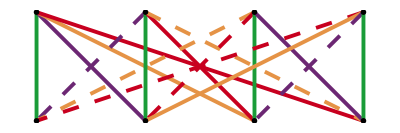

```mathematica
GraphAdinkra[Q]
```

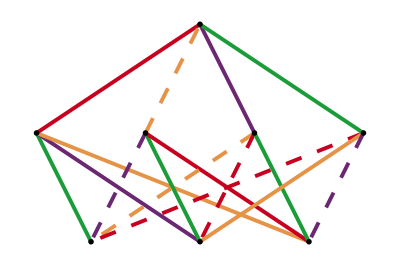

```mathematica
GraphAdinkra[Q,buildrules[{{8},{1,2,3,4},{5,6,7}}]]
```

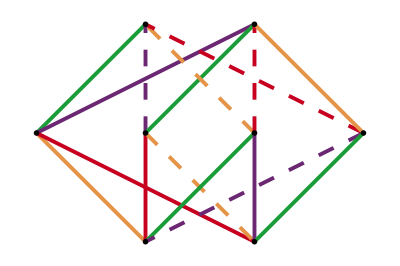

```mathematica
GraphAdinkra[Q,buildrules[{{5,6},{1,2,3,4},{7,8}}]]
```

```mathematica
GenerateAdinkraData[Q,Orthogonal]
```

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], L, R, GALR, GARL, V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = Q

{Null}

```mathematica
PrintAllGALR[Q]
```

{(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2)}

```mathematica
PrintAllGARL[Q]
```

{(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2)}

```mathematica
GenerateCoeffs[Q]
```

{LCoeffs, RCoeffs, GALRCoeffs, GARLCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, and VtildePMCoeffs are loaded for Rep = Q}

```mathematica
PrintGALRBasis[Q][1,1]
```

2 I_4

```mathematica
PrintVtildeBasis[Q][1,2]
```

-α_2

```mathematica
PrintGALRBasis[Q][1,2]
```

0

### Q̃: a base representation built in to Adinkra.m (((Q̃)_I)_i)^(ĵ)= {(), (OverBar[23])(12)(34), (OverBar[12])(13)(24), (OverBar[13])(14)(23)} = {I, i β^3, -i β^2, -i β^1} = {I, ĩ, j̃, k̃}

```mathematica
PrintAllL[Qtilde]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)}

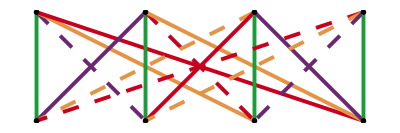

```mathematica
GraphAdinkra[Qtilde]
```

### CM

```mathematica
L[CM]={ ({{1, 0, 0, 0}, {0, 0, 0, -1}, {0, 1, 0, 0}, {0, 0, -1, 0}}),({{0, 1, 0, 0}, {0, 0, 1, 0}, {-1, 0, 0, 0}, {0, 0, 0, -1}}),({{0, 0, 1, 0}, {0, -1, 0, 0}, {0, 0, 0, -1}, {1, 0, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}})};
```

```mathematica
L[CM] == L[362511]
```

True

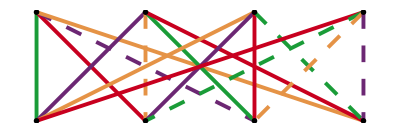

```mathematica
GraphAdinkra[CM]
```

### TM

```mathematica
L[TM]={ ({{1, 0, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}, {0, -1, 0, 0}}),({{0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, -1, 0}, {1, 0, 0, 0}}),({{0, 0, 1, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, -1}}),({{0, 0, 0, 1}, {0, -1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}})};
```

```mathematica
L[TM] == L[553212]
```

True

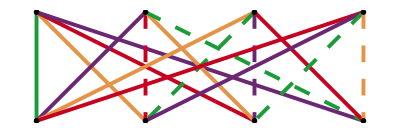

```mathematica
GraphAdinkra[TM]
```

### VM

```mathematica
L[VM]={ ({{0, 1, 0, 0}, {0, 0, 0, -1}, {1, 0, 0, 0}, {0, 0, -1, 0}}),({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, -1, 0, 0}, {0, 0, 0, -1}}),({{0, 0, 0, 1}, {0, 1, 0, 0}, {0, 0, 1, 0}, {1, 0, 0, 0}}),({{0, 0, 1, 0}, {-1, 0, 0, 0}, {0, 0, 0, -1}, {0, 1, 0, 0}})};
```

```mathematica
L[VM] == L[-342412]
```

True

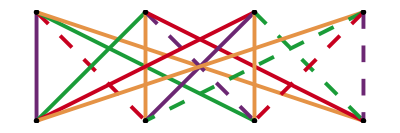

```mathematica
GraphAdinkra[VM]
```

### VM1

```mathematica
L[CM]={ ({{1, 0, 0, 0}, {0, 0, 0, -1}, {0, 1, 0, 0}, {0, 0, -1, 0}}),({{0, 1, 0, 0}, {0, 0, 1, 0}, {-1, 0, 0, 0}, {0, 0, 0, -1}}),({{0, 0, 1, 0}, {0, -1, 0, 0}, {0, 0, 0, -1}, {1, 0, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}})};
```

```mathematica
L[CM] == L[362511]
```

True

```mathematica
GraphAdinkra[CM]
```

-Graphics-

### cis adinkra

```mathematica
L[cis] = L[111712];
```

```mathematica
PrintAllL[cis]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)}

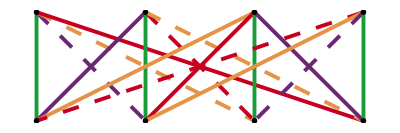

```mathematica
GraphAdinkra[cis]
```

### trans- adinkra

```mathematica
L[trans] = L[111112];
```

```mathematica
PrintAllL[trans]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
GraphAdinkra[trans]
```

-Graphics-

### L[-734262]

```mathematica
L[-734262]
```

{{{-1,0,0,0},{0,0,0,-1},{0,0,-1,0},{0,1,0,0}},{{0,0,0,-1},{1,0,0,0},{0,-1,0,0},{0,0,-1,0}},{{0,-1,0,0},{0,0,-1,0},{0,0,0,1},{-1,0,0,0}},{{0,0,-1,0},{0,1,0,0},{1,0,0,0},{0,0,0,1}}}

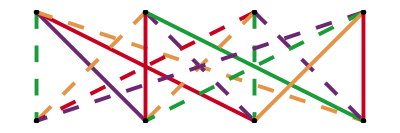

```mathematica
GraphAdinkra[-734262]
```

```mathematica
GenerateAdinkraData[-734262,Orthogonal]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = -734262

{Null}

```mathematica
PrintAllGALR[-734262]
```

{(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2)}

```mathematica
PrintAllGARL[-734262]
```

{(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2)}

### AdinkraPreliminaryReport[Rep] prints preliminary data to see if we want to proceed with analysis

```mathematica
GraphAdinkra[CM]
```

-Graphics-

```mathematica
GenerateAdinkraData[CM,Orthogonal]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = CM

{Null}

```mathematica
PrintAllGARL[CM]
```

{(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2)}

```mathematica
AdinkraReport[CM,1]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

N = 4
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
chi0 = 1, (ncis = 1, ntrans = 0)
LinearlyIndependent[V] = {{c[1, 2], c[1, 3], c[1, 4]}, {c[1, 4], -c[1, 3]}, {c[1, 2]}} == {{0, 0, 0}, {0, 0}, {0}}
LinearlyIndependent[Vtilde] = {{c[1, 2], c[1, 3], c[1, 4]}, {-c[1, 4], c[1, 3]}, {-c[1, 2]}} == {{0, 0, 0}, {0, 0}, {0}}

```mathematica
AdinkraPreliminaryReport[OnShellCM]
```

Rep = OnShellCM
N = 4
dbosons x dfermions = 2 × 4
GATest = False
InverseTest = R is not a square matrix
TransposeTest = True
chi0 = 0, (ncis = 1/4, ntrans = 1/4)

```mathematica
AdinkraReport[trans,0]
```

Part::partd: Part specification R[trans]⟦1,1⟧ is longer than depth of object.

N = 4

dbosons x dfermions = 4 × 4

Incorrect Dimensions

$Aborted

```mathematica
AdinkraPreliminaryReportO[cis]
```

Rep = cis
N = 4
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
chi0 = 1, (ncis = 1, ntrans = 0)

```mathematica
AdinkraPreliminaryReport[-734262]
```

Rep = -734262
N = 4
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
chi0 = -1, (ncis = 0, ntrans = 1)

Need to use AdinkraPreliminaryReportO[-734262] as never stored the R matrices for this Rep

```mathematica
AdinkraPreliminaryReportO[-734262]
```

Rep = -734262
N = 4
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
chi0 = -1, (ncis = 0, ntrans = 1)

### GenerateData

```mathematica
GenerateAdinkraData[Q,Orthogonal]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = Q

{Null}

```mathematica
GenerateCoeffs[Q]
```

{LCoeffs, RCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, and VtildePMCoeffs are loaded for Rep = Q}

```mathematica
GenerateAdinkraData[Qtilde,Orthogonal]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = Qtilde

{Null}

```mathematica
GenerateCoeffs[Qtilde]
```

{LCoeffs, RCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, and VtildePMCoeffs are loaded for Rep = Qtilde}

```mathematica
GenerateAdinkraData[CM,Orthogonal]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = CM

{Null}

```mathematica
GenerateCoeffs[CM]
```

{LCoeffs, RCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, and VtildePMCoeffs are loaded for Rep = CM}

```mathematica
GenerateAdinkraData[TM,Orthogonal]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = TM

{Null}

```mathematica
GenerateCoeffs[TM]
```

{LCoeffs, RCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, and VtildePMCoeffs are loaded for Rep = TM}

```mathematica
GenerateAdinkraData[VM,Orthogonal]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = VM

{Null}

```mathematica
GenerateCoeffs[VM]
```

{LCoeffs, RCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, and VtildePMCoeffs are loaded for Rep = VM}

```mathematica
GenerateAdinkraData[ID]
```

IncorrectDimensions, No Data Generated

```mathematica
GenerateCoeffs[ID] (* Need to fix this, shouldn't generate anything *)
```

Outer::heads: Heads List and ωmatrix[1/2] at positions 3 and 2 are expected to be the same.

ArrayFlatten::depth: The ArrayDepth of the expression at position 1 of ArrayFlatten[Outer[Times,ωmatrix[1/2][1],{{ⅈ,0,0,0},{0,-ⅈ,0,0},{0,0,-ⅈ,0},{0,0,0,ⅈ}}]] must be at least equal to the specified rank 2. (The rank is given by the optional second argument, which defaults to 2.)

Outer::heads: Heads List and ωmatrix[1/2] at positions 3 and 2 are expected to be the same.

ArrayFlatten::depth: The ArrayDepth of the expression at position 1 of ArrayFlatten[Outer[Times,ωmatrix[1/2][1],{{0,ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,ⅈ},{0,0,ⅈ,0}}]] must be at least equal to the specified rank 2. (The rank is given by the optional second argument, which defaults to 2.)

Outer::heads: Heads List and ωmatrix[1/2] at positions 3 and 2 are expected to be the same.

General::stop: Further output of Outer::heads will be suppressed during this calculation.

ArrayFlatten::depth: The ArrayDepth of the expression at position 1 of ArrayFlatten[Outer[Times,ωmatrix[1/2][1],{{0,0,-ⅈ,0},{0,0,0,ⅈ},{-ⅈ,0,0,0},{0,ⅈ,0,0}}]] must be at least equal to the specified rank 2. (The rank is given by the optional second argument, which defaults to 2.)

General::stop: Further output of ArrayFlatten::depth will be suppressed during this calculation.

Part::partd: Part specification Vtilde[ID]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of Vtilde[ID] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{RCoeffs, VtildeCoeffs, and VtildePMCoeffs are loaded for Rep = ID}

```mathematica
GenerateAdinkraData[OnShellCM]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = OnShellCM

```mathematica
GenerateAdinkraData[cis,Orthogonal]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = cis

{Null}

```mathematica
GenerateCoeffs[cis]
```

{LCoeffs, RCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, and VtildePMCoeffs are loaded for Rep = cis}

```mathematica
GenerateAdinkraData[trans,Orthogonal]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = trans

{Null}

```mathematica
GenerateCoeffs[trans]
```

{LCoeffs, RCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, and VtildePMCoeffs are loaded for Rep = trans}

```mathematica
GenerateAdinkraData[-734262,Orthogonal]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = -734262

{Null}

```mathematica
GenerateCoeffs[-734262]
```

{LCoeffs, RCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, and VtildePMCoeffs are loaded for Rep = -734262}

### Reports

```mathematica
AdinkraReport[ID,3]
```

N = 4

dbosons x dfermions = 2 × 4

Incorrect Dimensions

$Aborted

```mathematica
AdinkraReport[Q,3]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

N = 4
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
chi0 = -1, (ncis = 0, ntrans = 1)
LinearlyIndependent[V] = {{c[1, 2], c[1, 3], c[1, 4]}, {-c[1, 4], c[1, 3]}, {-c[1, 2]}} == {{0, 0, 0}, {0, 0}, {0}}
LinearlyIndependent[Vtilde] = {{c[1, 2], c[1, 3], c[1, 4]}, {c[1, 4], -c[1, 3]}, {c[1, 2]}} == {{0, 0, 0}, {0, 0}, {0}}
2^(-1+N) distinct ζ_I;    2^(-2+N) distinct |(ζ̃)_I|
2^(-1+N) distinct (ζ̃)_I;    2^(-2+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True

```mathematica
AdinkraReport[Q,3]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

N = 4
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
chi0 = -1, (ncis = 0, ntrans = 1)
LinearlyIndependent[V] = {{c[1, 2], c[1, 3], c[1, 4]}, {-c[1, 4], c[1, 3]}, {-c[1, 2]}} == {{0, 0, 0}, {0, 0}, {0}}
LinearlyIndependent[Vtilde] = {{c[1, 2], c[1, 3], c[1, 4]}, {c[1, 4], -c[1, 3]}, {c[1, 2]}} == {{0, 0, 0}, {0, 0}, {0}}
2^(-1+N) distinct ζ_I;    2^(-2+N) distinct |(ζ̃)_I|
2^(-1+N) distinct (ζ̃)_I;    2^(-2+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True

```mathematica
AdinkraReport[Q,8]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

N = 4
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
chi0 = -1, (ncis = 0, ntrans = 1)
LinearlyIndependent[V] = {{c[1, 2], c[1, 3], c[1, 4]}, {-c[1, 4], c[1, 3]}, {-c[1, 2]}} == {{0, 0, 0}, {0, 0}, {0}}
LinearlyIndependent[Vtilde] = {{c[1, 2], c[1, 3], c[1, 4]}, {c[1, 4], -c[1, 3]}, {c[1, 2]}} == {{0, 0, 0}, {0, 0}, {0}}
2^(-1+N) distinct ζ_I;    2^(-2+N) distinct |(ζ̃)_I|
2^(-1+N) distinct (ζ̃)_I;    2^(-2+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
Allsu2MutuallyCommute = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True
soNTest[VsoNPM[-1]] = True
soNTest[VsoNPM[1]] = True
soNTest[VtildesoNPM[-1]] = True
soNTest[VtildesoNPM[1]] = True
su2Test[VsoNPM[-1]] = True
su2Test[VsoNPM[1]] = True
VPM[1] and VPM[-1] mutually commute = True
su2Test[VtildesoNPM[-1]] = True
su2Test[VtildesoNPM[1]] = True
VtildePM[1] and VtildePM[-1] mutually commute = True

```mathematica
AdinkraReport[OnShellCM]
```

N = 4
dbosons x dfermions = 2 × 4
GATest = False
InverseTest = R is not a square matrix
TransposeTest = True
chi0 = 0, (ncis = 1/4, ntrans = 1/4)

```mathematica
AdinkraReport[OnShellCM]
```

N = 4
dbosons x dfermions = 2 × 4
GATest = False
InverseTest = R is not a square matrix
TransposeTest = True
chi0 = 0, (ncis = 1/4, ntrans = 1/4)

```mathematica
AdinkraFullReport[OnShellCM]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

N = 4
dbosons x dfermions = 2 × 4
GATest = False
InverseTest = R is not a square matrix
TransposeTest = True
chi0 = 0, (ncis = 1/4, ntrans = 1/4)
LinearlyIndependent[V] = {{c[1, 2], c[1, 3], c[1, 4]}, {c[1, 4], c[2, 4]}, {c[3, 4]}} == {{0, 0, 0}, {0, 0}, {0}}
LinearlyIndependent[Vtilde] = {{c[1, 2], c[1, 3], 0}, {0, c[1, 3]}, {-c[1, 2]}} == {{0, 0, 0}, {0, 0}, {0}}
ZetaGen has singular elements
ZetatildeGen has singular elements
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = False
AllsoNTest = False
Allsu2MutuallyCommute = False
soNTest[VsoN] = False
soNTest[VtildesoN] = False
soNTest[VsoNPM[-1]] = False
soNTest[VsoNPM[1]] = True
soNTest[VtildesoNPM[-1]] = False
soNTest[VtildesoNPM[1]] = False
su2Test[VsoNPM[-1]] = False
su2Test[VsoNPM[1]] = True
VPM[1] and VPM[-1] mutually commute = True
su2Test[VtildesoNPM[-1]] = False
su2Test[VtildesoNPM[1]] = False
VtildePM[1] and VtildePM[-1] mutually commute = True

```mathematica
AdinkraFullReport[TM]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

N = 4
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
chi0 = -1, (ncis = 0, ntrans = 1)
LinearlyIndependent[V] = {{c[1, 2], c[1, 3], c[1, 4]}, {-c[1, 4], c[1, 3]}, {-c[1, 2]}} == {{0, 0, 0}, {0, 0}, {0}}
LinearlyIndependent[Vtilde] = {{c[1, 2], c[1, 3], c[1, 4]}, {c[1, 4], -c[1, 3]}, {c[1, 2]}} == {{0, 0, 0}, {0, 0}, {0}}
2^(-1+N) distinct ζ_I;    2^(-2+N) distinct |(ζ̃)_I|
2^(-1+N) distinct (ζ̃)_I;    2^(-2+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
Allsu2MutuallyCommute = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True
soNTest[VsoNPM[-1]] = True
soNTest[VsoNPM[1]] = True
soNTest[VtildesoNPM[-1]] = True
soNTest[VtildesoNPM[1]] = True
su2Test[VsoNPM[-1]] = True
su2Test[VsoNPM[1]] = True
VPM[1] and VPM[-1] mutually commute = True
su2Test[VtildesoNPM[-1]] = True
su2Test[VtildesoNPM[1]] = True
VtildePM[1] and VtildePM[-1] mutually commute = True

```mathematica
V[VM][[1,2]]==V[VM][[3,4]]
```

True

```mathematica
V[VM][[1,2]] == 2VsoN[VM][[1,2]]
```

True

```mathematica
FunctionList[AdinkraEssentials]
```

IndexRange[AdinkraEssentials][Index], Index = p1, II, ReportLevel, or pm

***IMPORTANT****: Default Settings are VScaleFactor = VtildeScaleFactor = -I, VsoNScaleFactor = -I/(2 VsoNScaleFactor), VtildesoNScaleFactor = -I/(2 VtildesoNScaleFactor)

Reports: AdinkraReport[Rep,ReportLevel], AdinkraPreliminaryReport[L,R], AdinkraPreliminaryReport[Rep], AdinkraPreliminaryReportO[Rep], AdinkraHoloMonoReport[Rep], AdinkraSummaryReport[Rep], AdinkraFullReport[Rep]

Basic Functions: nMatrices[Matrices], nRows[Matrices], nColumns[Matrices], Commute[Matrix1,Matrix2], NColors[Rep], NColors[L,R], dmin[N], dbosons[Rep], dbosons[L,R], dfermions[Rep], dfermions[L,R], WordW[{p1,p2,...,pN}]

Intense Calculations: Gadget[Rep1,Rep2], BosonGadget[Rep1,Rep2], ListOfIdenticalMonoOrHolo[MonoOrHolo,Rep], NumDistinctHoloOrMono[HoloOrMono,Rep]

Print Functions: PrintL[Rep][II], PrintR[Rep][II],PrintV[Rep][II,JJ], PrintVtilde[Rep][II,JJ], PrintZetaGen[Rep][II], PrintHoloraumy[Rep][{p1,p2,...,pN}], PrintMonodromy[Rep][{p1,p2,...,pN}],PrintZetatildeGen[Rep][II], PrintHoloraumytilde[Rep][{p1,p2,...,pN}], PrintMonodromytilde[Rep][{p1,p2,...,pN}], PrintVtildePM[pm][Rep][II,JJ], PrintVtildePM[pm][Rep][II,JJ], PrintAllL[Rep], PrintAllR[Rep],PrintAllV[Rep], PrintAllVtilde[Rep], PrintAllZetaGen[Rep], PrintAllHoloraumy[Rep], PrintAllMonodromy[Rep],PrintAllZetatildeGen[Rep], PrintAllHoloraumytilde[Rep], PrintAllMonodromytilde[Rep], PrintAllVtildePM[pm][Rep], PrintAllVtildePM[pm][Rep], ,PrintSigmaProduct[Matrix], PrintLSigmaProduct[Rep], PrintRSigmaProduct[Rep]

Test Functions: CorrectDimensions[Rep], CorrectDimensions[L,R], TransposeTest[Rep], TransposeTest[L,R], InverseTest[Rep], InverseTest[L,R], RO[Rep], Chi0Report[L,R], GATest[Rep], GATest[L,R], soNTest[Matrices], su2Test[MgenPM[pm]][Rep], MutuallyCommuteTest[M1,M2], LinearlyIndependent[Mgen]

Data generated by GenerateAdinkraData[Rep], GenerateAdinkraData[Rep,Orthogonal], GenerateAdinkraDataO[Rep], GenerateAdinkraData[Rep,L], or GenerateAdinkraData[Rep,L,R]:
L[Rep], R[Rep], chi0[Rep], ncis[Rep], ntrans[Rep], V[Rep], Vtilde[Rep], VsoN[Rep], VtildesoN[Rep], ZetaGen[Rep], Holoraumy[Rep], Monodromy[Rep], ZetatildeGen[Rep], Holoraumytilde[Rep], Monodromytilde[Rep], VPM[pm][Rep], VtildePM[pm][Rep], VsoNPM[pm][Rep], VtildesoNPM[pm][Rep] cSoln[V[Rep]], cSoln[Vtilde[Rep]]

****************************************************************************************
****************************************************************************************

#### When the LinearlyIndependent function does not give True, the output below is read as follows: VPM[-1][CM][[2,3]] + VPM[-1][CM][[1,4]] = 0 => VPM[-1][CM][[2,3]] = - VPM[-1][CM][[1,4]] VPM[-1][CM][[2,4]] - VPM[-1][CM][[1,3]] = 0 => VPM[-1][CM][[2,4]] = VPM[-1][CM][[1,3]] VPM[-1][CM][[3,4]] + VPM[-1][CM][[1,2]] = 0 => VPM[-1][CM][[3,4]] = - VPM[-1][CM][[1,2]]

```mathematica
LinearlyIndependent[VPM[-1][CM]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c[1,2],c[1,3],c[1,4]},{c[1,4],-c[1,3]},{c[1,2]}}=={{0,0,0},{0,0},{0}}

```mathematica
PrintAllVPM[-1][CM]
```

{(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0)}

### Define BC4ColorPerm[n,a,μ,A]:=(-1)^n((H^a)_I)^K((S_3^μ)_K)^L((𝒱^A)_L)^J H^a= { (),(OverBar[12]),(OverBar[13]),(OverBar[23]) ,(OverBar[1]),(OverBar[2]),(OverBar[3]),(OverBar[123])} , sign flips on three elements S^μ = { (), (12), (13), (23), (123), (132) }:, S_3 permutation group: 𝒱^A= {(), (12)(34), (13)(24), (14)(23) }, the vierergruppe:

#### Here we are using the BC4Tools package, so lets display the function list to see what we have to use

```mathematica
FunctionList[BC4Tools]
```

IndexRange[BC4Tools][Index], Index = n, a, μ, A, II, or tt

Functions: 
HPerm[a], H[[a]], S3Perm[μ], S3[[μ]], VierPerm[A], Vier[[A]], BC4[[n,a,μ,A,II,JJ]] , BC4Perm[n,a,μ,A][[II,JJ]], QuaternionTestIJK[Quat], QuaternionTestKJI[Quat], Digit[Num,Pow], ell[Rep][tt,a][II,JJ], kappa[Rep][ti,a][II,JJ], IellABColor[Rep][[a]], PrintIell[Rep][[a]], IellABCode[Rep][[a]], AntisymmetryCheck[Object1], BC4Color[n,a,μ,A][L], BC4ColorPerm[n,a,μ,A][L],BC4Boson[n,a,μ,A][L],BC4BosonPerm[n,a,μ,A][L], HList,S3List,VierList,PrintBC4Perm[n,a,μ,A],PrintBC4BosonPerm[n,a,μ,A],PrintBC4FermionPerm[n,a,μ,A],PrintBC4ColorPerm[n,a,μ,A],L[Q],L[Qtilde],L[RepCode]

****************************************************************************************
****************************************************************************************

#### Use Index Range to display the valid ranges for a given type of index listed in the FunctionList

```mathematica
IndexRange[BC4Tools][n]
```

1,2 for Table, Integers for Perm

```mathematica
IndexRange[BC4Tools][a]
```

1,2,3,4,5,6,7,8 for Table, 0,12,13,23,1,2,3,123 for Perm

```mathematica
IndexRange[BC4Tools][μ]
```

1,2,3,4,5,6 for Table, 0,12,13,23,123,132 for Perm

```mathematica
IndexRange[BC4Tools][A]
```

1,2,3,4 for Table, 0,1234,1324,1423 for Perm

#### Some Permutation Matrices

```mathematica
S3Perm[123].VierPerm[1423]//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0)

```mathematica
BC4Perm[0,12,123,1423]//MatrixForm
```

(0 | -1 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0
1 | 0 | 0 | 0)

```mathematica
BC4Perm[0,12,123,1423][[1,2]]L[Q][[2]]
```

{{0,1,0,0},{-1,0,0,0},{0,0,0,1},{0,0,-1,0}}

```mathematica
S3Perm[132]//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1)

#### We are using BC4ColorPerm, rather than BC4Color so use the appropriate indices

```mathematica
L[NewQ]=BC4ColorPerm[-1,12,123,1423][L[Q]];
```

```mathematica
PrintAllL[NewQ]
```

{(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

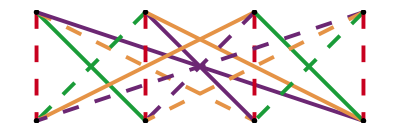

```mathematica
GraphAdinkra[NewQ]
```

#### Compare to Q, the above is a permutation of the colors as encoded in PrintBC4ColorPerm below read right to left: then flopping (swapping) colors 1 and 4 and 2 and 3: (14)(23) then flopping color 1 to 2 to 3 to 1: (123) ---> (142) 1 to 4 (green to red, as in what was green in Q is now red in NewQ), 4 to 2 (red to becomes purple) 2 to 1 (purple becomes green) orange stays orange the flipping (switching the sign of) colors 3 and 4 (orange and red): (OverBar[34])

```mathematica
PrintBC4ColorPerm[-1,12,123,1423]
```

((**OverBar[34]**)**(123)(14)(23)()_I)^J

```mathematica
GraphAdinkra[Q]
```

-Graphics-

```mathematica
GraphAdinkra[NewQ]
```

-Graphics-

### In terms of the Table indices: BC4Color[n,a,μ,A][L[Rep]] := ((BC_4^mbνB)_I)^J((L_J^(Rep))_i)^(ĵ)= (-1)^m((H^b)_I)^K((S_3^ν)_K)^L((𝒱^B)_L)^J((L_J^(Rep))_i)^(ĵ) BC4Boson[n,a,μ,A][L[Rep]] := ((BC_4^mbνB)_i)^j((L_I^(Rep))_j)^(ĵ)= (-1)^m((H^b)_i)^k((S_3^ν)_k)^p((𝒱^B)_p)^j((L_I^(Rep))_j)^(ĵ) for n = 1 we have the minus sign b=2 is the sign flip (OverBar[12]), so put these together we have -(OverBar[12])=(OverBar[34]) μ=5 is the Permutation (123) A=4 is the Vierergruppe element (14)(23) so we should use BC4Color[1,2,5,4]

```mathematica
IndexRange[BC4Tools][n]
```

1,2 for Table, Integers for Perm

```mathematica
IndexRange[BC4Tools][a]
```

1,2,3,4,5,6,7,8 for Table, 0,12,13,23,1,2,3,123 for Perm

```mathematica
IndexRange[BC4Tools][μ]
```

1,2,3,4,5,6 for Table, 0,12,13,23,123,132 for Perm

```mathematica
IndexRange[BC4Tools][A]
```

1,2,3,4 for Table, 0,1234,1324,1423 for Perm

```mathematica
L[NewQTable]=BC4Color[1,2,5,4][L[Q]];
```

```mathematica
PrintAllL[NewQTable]
```

{(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

```mathematica
L[NewQTable]==L[NewQ]
```

True

```mathematica
GraphAdinkra[NewQTable]
```

-Graphics-

```mathematica
GraphAdinkra[Q]
```

-Graphics-

```mathematica
GraphAdinkra[NewQTable]
GraphAdinkra[NewQ]
```

-Graphics-

-Graphics-

### Isometry BC4Color and BC4Boson transformations on Q

#### Q_I

```mathematica
LBP = {0,0,0,0};
LCP = {0,0,0,0};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Q]]];
GraphAdinkra[Local]
L[Local] == L[Q]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
```

-Graphics-

True

(()_i)^j (()_I)^J

#### BC4Boson: (OverBar[1234]); BC4Color: (OverBar[1234])

```mathematica
LBP = {-1,0,0,0};
LCP = {-1,0,0,0};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Q]]];
GraphAdinkra[Local]
L[Local] == L[Q]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

(**OverBar[1234]**()_i)^j (**OverBar[1234]**()_I)^J

(\text{**}\overline{1234}\text{**})_i{}^j (\text{**}\overline{1234}\text{**})_I{}^J

#### BC4Boson: (OverBar[13])(12)(34); BC4Color: (OverBar[13])(12)(34)

```mathematica
LBP = {0,13,0,1234};
LCP = {0,13,0,1234};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Q]]];
GraphAdinkra[Local]
L[Local] == L[Q]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

((**OverBar[13]**)**(12)(34)()_i)^j ((**OverBar[13]**)**(12)(34)()_I)^J

\text{((}\text{**}\overline{13}\text{**})\text{**}\text{(12)(34)})_i{}^j \text{((}\text{**}\overline{13}\text{**})\text{**}\text{(12)(34)})_I{}^J

#### BC4Boson: (OverBar[24])(12)(34); BC4Color: (OverBar[24])(12)(34)

```mathematica
LBP = {-1,13,0,1234};
LCP = {-1,13,0,1234};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Q]]];
GraphAdinkra[Local]
L[Local] == L[Q]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

((**OverBar[24]**)**(12)(34)()_i)^j ((**OverBar[24]**)**(12)(34)()_I)^J

\text{((}\text{**}\overline{24}\text{**})\text{**}\text{(12)(34)})_i{}^j \text{((}\text{**}\overline{24}\text{**})\text{**}\text{(12)(34)})_I{}^J

#### BC4Boson: (OverBar[23])(13)(24); BC4Color: (OverBar[23])(13)(24)

```mathematica
LBP = {0,23,0,1324};
LCP = {0,23,0,1324};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Q]]];
GraphAdinkra[Local]
L[Local] == L[Q]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

((**OverBar[23]**)**(13)(24)()_i)^j ((**OverBar[23]**)**(13)(24)()_I)^J

\text{((}\text{**}\overline{23}\text{**})\text{**}\text{(13)(24)})_i{}^j \text{((}\text{**}\overline{23}\text{**})\text{**}\text{(13)(24)})_I{}^J

#### BC4Boson: (OverBar[14])(13)(24); BC4Color: (OverBar[14])(13)(24)

```mathematica
LBP = {-1,23,0,1324};
LCP = {-1,23,0,1324};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Q]]];
GraphAdinkra[Local]
L[Local] == L[Q]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

((**OverBar[14]**)**(13)(24)()_i)^j ((**OverBar[14]**)**(13)(24)()_I)^J

\text{((}\text{**}\overline{14}\text{**})\text{**}\text{(13)(24)})_i{}^j \text{((}\text{**}\overline{14}\text{**})\text{**}\text{(13)(24)})_I{}^J

#### BC4Boson: (OverBar[12])(14)(23); BC4Color: (OverBar[12])(14)(23)

```mathematica
LBP = {0,12,0,1423};
LCP = {0,12,0,1423};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Q]]];
GraphAdinkra[Local]
L[Local] == L[Q]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

((**OverBar[12]**)**(14)(23)()_i)^j ((**OverBar[12]**)**(14)(23)()_I)^J

\text{((}\text{**}\overline{12}\text{**})\text{**}\text{(14)(23)})_i{}^j \text{((}\text{**}\overline{12}\text{**})\text{**}\text{(14)(23)})_I{}^J

#### BC4Boson: (OverBar[34])(14)(23); BC4Color: (OverBar[34])(14)(23)

```mathematica
LBP = {-1,12,0,1423};
LCP = {-1,12,0,1423};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Q]]];
GraphAdinkra[Local]
L[Local] == L[Q]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

((**OverBar[34]**)**(14)(23)()_i)^j ((**OverBar[34]**)**(14)(23)()_I)^J

\text{((}\text{**}\overline{34}\text{**})\text{**}\text{(14)(23)})_i{}^j \text{((}\text{**}\overline{34}\text{**})\text{**}\text{(14)(23)})_I{}^J

### Isometry BC4Color and BC4Boson transformations on Q̃

#### (Q̃)_I

```mathematica
LBP = {0,0,0,0};
LCP = {0,0,0,0};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Qtilde]]];
GraphAdinkra[Local]
L[Local] == L[Qtilde]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

(()_i)^j (()_I)^J

\left()_i{}^j\right. \left()_I{}^J\right.

#### BC4Boson: (OverBar[1234]); BC4Color: (OverBar[1234])

```mathematica
LBP = {-1,0,0,0};
LCP = {-1,0,0,0};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Qtilde]]];
GraphAdinkra[Local]
L[Local] == L[Qtilde]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

(**OverBar[1234]**()_i)^j (**OverBar[1234]**()_I)^J

(\text{**}\overline{1234}\text{**})_i{}^j (\text{**}\overline{1234}\text{**})_I{}^J

#### BC4Boson: (OverBar[23])(12)(34); BC4Color: (OverBar[13])(12)(34)

```mathematica
LBP = {0,23,0,1234};
LCP = {0,13,0,1234};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Qtilde]]];
GraphAdinkra[Local]
L[Local] == L[Qtilde]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

((**OverBar[13]**)**(12)(34)()_I)^J ((**OverBar[23]**)**(12)(34)()_i)^j

\text{((}\text{**}\overline{23}\text{**})\text{**}\text{(12)(34)})_i{}^j \text{((}\text{**}\overline{13}\text{**})\text{**}\text{(12)(34)})_I{}^J

#### BC4Boson: (OverBar[14])(12)(34); BC4Color: (OverBar[24])(12)(34)

```mathematica
LBP = {-1,23,0,1234};
LCP = {-1,13,0,1234};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Qtilde]]];
GraphAdinkra[Local]
L[Local] == L[Qtilde]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

((**OverBar[14]**)**(12)(34)()_i)^j ((**OverBar[24]**)**(12)(34)()_I)^J

\text{((}\text{**}\overline{14}\text{**})\text{**}\text{(12)(34)})_i{}^j \text{((}\text{**}\overline{24}\text{**})\text{**}\text{(12)(34)})_I{}^J

#### BC4Boson: (OverBar[12])(13)(24); BC4Color: (OverBar[14])(13)(24)

```mathematica
LBP = {0,12,0,1324};
LCP = {-1,23,0,1324};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Qtilde]]];
GraphAdinkra[Local]
L[Local] == L[Qtilde]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

((**OverBar[12]**)**(13)(24)()_i)^j ((**OverBar[14]**)**(13)(24)()_I)^J

\text{((}\text{**}\overline{12}\text{**})\text{**}\text{(13)(24)})_i{}^j \text{((}\text{**}\overline{14}\text{**})\text{**}\text{(13)(24)})_I{}^J

#### BC4Boson: (OverBar[34])(13)(24); BC4Color: (OverBar[23])(13)(24)

```mathematica
LBP = {-1,12,0,1324};
LCP = {0,23,0,1324};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Qtilde]]];
GraphAdinkra[Local]
L[Local] == L[Qtilde]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

((**OverBar[23]**)**(13)(24)()_I)^J ((**OverBar[34]**)**(13)(24)()_i)^j

\text{((}\text{**}\overline{34}\text{**})\text{**}\text{(13)(24)})_i{}^j \text{((}\text{**}\overline{23}\text{**})\text{**}\text{(13)(24)})_I{}^J

#### BC4Boson: (OverBar[13])(14)(23); BC4Color: (OverBar[12])(14)(23)

```mathematica
LBP = {0,13,0,1423};
LCP = {0,12,0,1423};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Qtilde]]];
GraphAdinkra[Local]
L[Local] == L[Qtilde]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

((**OverBar[12]**)**(14)(23)()_I)^J ((**OverBar[13]**)**(14)(23)()_i)^j

\text{((}\text{**}\overline{13}\text{**})\text{**}\text{(14)(23)})_i{}^j \text{((}\text{**}\overline{12}\text{**})\text{**}\text{(14)(23)})_I{}^J

#### BC4Boson: (OverBar[24])(14)(23); BC4Color: (OverBar[34])(14)(23)

```mathematica
LBP = {-1,13,0,1423};
LCP = {-1,12,0,1423};
L[Local] = BC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]][BC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]][L[Qtilde]]];
GraphAdinkra[Local]
L[Local] == L[Qtilde]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]
PrintBC4BosonPerm[LBP[[1]],LBP[[2]],LBP[[3]],LBP[[4]]]PrintBC4ColorPerm[LCP[[1]],LCP[[2]],LCP[[3]],LCP[[4]]]//TeXForm
```

-Graphics-

True

((**OverBar[24]**)**(14)(23)()_i)^j ((**OverBar[34]**)**(14)(23)()_I)^J

\text{((}\text{**}\overline{24}\text{**})\text{**}\text{(14)(23)})_i{}^j \text{((}\text{**}\overline{34}\text{**})\text{**}\text{(14)(23)})_I{}^J

```mathematica
96*384
```

36864

```mathematica
48*8
```

384

### All 36864 N=4, d=4 valise adinkras ((L_I^(±aμAbν))_i)^(ĵ):=((BC_4^(±aμA))_i)^j((L_I^bν)_j)^(ĵ)=((BC_4^(±aμA))_i)^j((HS_3^bν)_I)^J ((Q_J)_j)^(ĵ) , (Ṽ)_IJ~α (ℓ-equivalence classes) (((L̃)_I^(±aμAbν))_i)^(ĵ):= ((BC_4^(±aμA))_i)^j(((L̃)_I^bν)_j)^(ĵ)=((BC_4^(±aμA))_i)^j((HS_3^bν)_I)^J (((Q̃)_J)_j)^(ĵ) , (Ṽ)_IJ~β (ℓ̃-equivalence classes) L[RepCode] := ((L_I^(±aμAbν))_i)^(ĵ) for RepCode = ±aμAbν1, (((L̃)_I^(±aμAbν))_i)^(ĵ)for RepCode= ±aμAbν2

```mathematica
PrintAllL[CM]
```

{(1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 1 | 0 | 0
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
0 | 0 | 1 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
0 | -1 | 0 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0)}

```mathematica
L[CM] == L[362511]
```

True

```mathematica
GraphAdinkra[CM]
```

-Graphics-

## N≠4, Various Representations

### 3-cube

#### Generating the Adinkras

```mathematica
Rep = ThreeHypercube;
```

```mathematica
L[Rep]={IdentityMatrix[4],I SigmaProduct[3,2],-I SigmaProduct[2,0]};
```

```mathematica
PrintLSigmaProduct[Rep]
```

{I⊗I,ⅈ σ_3⊗σ_2,-ⅈ σ_2⊗I}

```mathematica
AdinkraPreliminaryReportO[Rep]
```

Rep = ThreeHypercube
N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True

```mathematica
GenerateAdinkraDataO[Rep];
```

V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = ThreeHypercube

```mathematica
AdinkraHoloMonoReport[Rep]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True

```mathematica
AdinkraReport[Rep]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True

```mathematica
AdinkraFullReport[Rep]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True

```mathematica
PrintAllGALR[Rep]
```

{(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2)}

```mathematica
PrintAllGARL[Rep]
```

{(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2)}

#### Holoraumy: 8 distinct elements, Monodromy: 4 distinct elements

```mathematica
PrintAllHoloraumy[Rep]
```

{(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
PrintAllHoloraumy[ThreeHypercube]
```

{(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
PrintAllMonodromy[Rep]
```

{(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

### Another 3-cube

#### Generating the Adinkra

```mathematica
Rep = AnotherThreeHypercube;
```

```mathematica
L[Rep]={L[ThreeHypercube][[3]],L[ThreeHypercube][[1]],L[ThreeHypercube][[2]]};
```

```mathematica
PrintLSigmaProduct[Rep]
```

{-ⅈ σ_2⊗I,I⊗I,ⅈ σ_3⊗σ_2}

```mathematica
GenerateAdinkraDataO[Rep];
```

V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = AnotherThreeHypercube

```mathematica
AdinkraPreliminaryReport[Rep]
```

Rep = AnotherThreeHypercube
N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True

```mathematica
AdinkraReport[Rep,0]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True

```mathematica
AdinkraReport[Rep,1]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True

```mathematica
AdinkraReport[Rep,2]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True

```mathematica
AdinkraReport[Rep,3]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True

```mathematica
AdinkraReport[Rep,4]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
AllsoNTest = True

```mathematica
AdinkraReport[Rep,5]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
AllsoNTest = True

```mathematica
AdinkraReport[Rep,6]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True

```mathematica
AdinkraReport[Rep,7]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True

```mathematica
AdinkraReport[Rep,8]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True

```mathematica
AdinkraSummaryReport[Rep]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True

```mathematica
AdinkraFullReport[Rep]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True

#### Holoraumy: 8 distinct elements, Monodromy: 4 distinct elements

```mathematica
PrintAllHoloraumy[Rep]
```

{(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
PrintAllMonodromy[Rep]
```

{(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
PrintHoloraumy[Rep][{1,1,1}]
```

(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)

```mathematica
PrintMonodromy[Rep][{1,1,1}]
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

### Yet Another 3-cube

#### Generating the Adinkra

```mathematica
Rep = YetAnotherThreeHypercube;
```

```mathematica
L[Rep]={L[ThreeHypercube][[1]],L[ThreeHypercube][[3]],L[ThreeHypercube][[2]]};
```

```mathematica
PrintLSigmaProduct[Rep]
```

{I⊗I,-ⅈ σ_2⊗I,ⅈ σ_3⊗σ_2}

```mathematica
GenerateAdinkraDataO[Rep];
```

V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = YetAnotherThreeHypercube

```mathematica
AdinkraPreliminaryReport[Rep]
```

Rep = YetAnotherThreeHypercube
N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True

```mathematica
AdinkraReport[Rep]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True

```mathematica
AdinkraFullReport[Rep]
```

N = 3
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True

#### Holoraumy: 8 distinct elements, Monodromy: 4 distinct elements

```mathematica
PrintAllHoloraumy[Rep]
```

{(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
PrintAllMonodromy[Rep]
```

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

### The Tesseract or the 4-Hypercube

#### Generating the Adinkra

```mathematica
Rep = Tesseract;
```

```mathematica
L[Rep]={IdentityMatrix[8],SigmaMatrixProduct[0,L[ThreeHypercube][[2]]],SigmaMatrixProduct[3,L[ThreeHypercube][[3]]],SigmaMatrixProduct[1,L[ThreeHypercube][[3]]]};
```

```mathematica
PrintLSigmaProduct[Rep]
```

{I⊗I⊗I,ⅈ I⊗σ_3⊗σ_2,-ⅈ σ_3⊗σ_2⊗I,-ⅈ σ_1⊗σ_2⊗I}

```mathematica
GenerateAdinkraDataO[Rep];
```

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = Tesseract

```mathematica
AdinkraReport[Rep]
```

N = 4
dbosons x dfermions = 8 × 8
GATest = True
InverseTest = True
TransposeTest = True
chi0 = 0, (ncis = 1, ntrans = 1)

```mathematica
AdinkraFullReport[Rep]
```

N = 4
dbosons x dfermions = 8 × 8
GATest = True
InverseTest = True
TransposeTest = True
chi0 = 0, (ncis = 1, ntrans = 1)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
Allsu2MutuallyCommute = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True
soNTest[VsoNPM[-1]] = True
soNTest[VsoNPM[1]] = True
soNTest[VtildesoNPM[-1]] = True
soNTest[VtildesoNPM[1]] = True
su2Test[VsoNPM[-1]] = True
su2Test[VsoNPM[1]] = True
VPM[1] and VPM[-1] mutually commute = True
su2Test[VtildesoNPM[-1]] = True
su2Test[VtildesoNPM[1]] = True
VtildePM[1] and VtildePM[-1] mutually commute = True

#### Holoraumy: 16 distinct elements, Monodromy 8 distinct elements

```mathematica
PrintAllHoloraumy[Rep]
```

{(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
PrintAllMonodromy[Rep]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
FunctionList[AdinkraEssentials]
```

IndexRange[AdinkraEssentials][Index], Index = p1, II, ReportLevel, or pm

***IMPORTANT****: Default Settings are VScaleFactor = VtildeScaleFactor = -I, VsoNScaleFactor = -I/(2 VsoNScaleFactor), VtildesoNScaleFactor = -I/(2 VtildesoNScaleFactor)

Reports: AdinkraReport[Rep,ReportLevel], AdinkraPreliminaryReport[L,R], AdinkraPreliminaryReport[Rep], AdinkraPreliminaryReportO[Rep], AdinkraHoloMonoReport[Rep], AdinkraSummaryReport[Rep], AdinkraFullReport[Rep]

Basic Functions: nMatrices[Matrices], nRows[Matrices], nColumns[Matrices], Commute[Matrix1,Matrix2], NColors[Rep], NColors[L,R], dmin[N], dbosons[Rep], dbosons[L,R], dfermions[Rep], dfermions[L,R], WordW[{p1,p2,...,pN}]

Intense Calculations: Gadget[Rep1,Rep2], BosonGadget[Rep1,Rep2], ListOfIdenticalMonoOrHolo[MonoOrHolo,Rep], NumDistinctHoloOrMono[HoloOrMono,Rep]

Print Functions: PrintL[Rep][II], PrintR[Rep][II],PrintV[Rep][II,JJ], PrintVtilde[Rep][II,JJ], PrintZetaGen[Rep][II], PrintHoloraumy[Rep][{p1,p2,...,pN}], PrintMonodromy[Rep][{p1,p2,...,pN}],PrintZetatildeGen[Rep][II], PrintHoloraumytilde[Rep][{p1,p2,...,pN}], PrintMonodromytilde[Rep][{p1,p2,...,pN}], PrintVtildePM[pm][Rep][II,JJ], PrintVtildePM[pm][Rep][II,JJ], PrintAllL[Rep], PrintAllR[Rep],PrintAllV[Rep], PrintAllVtilde[Rep], PrintAllZetaGen[Rep], PrintAllHoloraumy[Rep], PrintAllMonodromy[Rep],PrintAllZetatildeGen[Rep], PrintAllHoloraumytilde[Rep], PrintAllMonodromytilde[Rep], PrintAllVtildePM[pm][Rep], PrintAllVtildePM[pm][Rep], ,PrintSigmaProduct[Matrix], PrintLSigmaProduct[Rep], PrintRSigmaProduct[Rep]

Test Functions: CorrectDimensions[Rep], CorrectDimensions[L,R], TransposeTest[Rep], TransposeTest[L,R], InverseTest[Rep], InverseTest[L,R], RO[Rep], Chi0Report[L,R], GATest[Rep], GATest[L,R], soNTest[Matrices], su2Test[MgenPM[pm]][Rep], MutuallyCommuteTest[M1,M2], LinearlyIndependent[Mgen]

Data generated by GenerateAdinkraData[Rep], GenerateAdinkraData[Rep,Orthogonal], GenerateAdinkraDataO[Rep], GenerateAdinkraData[Rep,L], or GenerateAdinkraData[Rep,L,R]:
L[Rep], R[Rep], chi0[Rep], ncis[Rep], ntrans[Rep], V[Rep], Vtilde[Rep], VsoN[Rep], VtildesoN[Rep], ZetaGen[Rep], Holoraumy[Rep], Monodromy[Rep], ZetatildeGen[Rep], Holoraumytilde[Rep], Monodromytilde[Rep], VPM[pm][Rep], VtildePM[pm][Rep], VsoNPM[pm][Rep], VtildesoNPM[pm][Rep] cSoln[V[Rep]], cSoln[Vtilde[Rep]]

****************************************************************************************
****************************************************************************************

```mathematica
ListOfIdenticalMonoOrHolo[Holoraumy,Rep]
```

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16}}

```mathematica
ListOfIdenticalMonoOrHolo[Monodromy,Rep]
```

{{1,1},{1,9},{2,2},{2,10},{3,3},{3,11},{4,4},{4,12},{5,5},{5,13},{6,6},{6,14},{7,7},{7,15},{8,8},{8,16},{9,1},{9,9},{10,2},{10,10},{11,3},{11,11},{12,4},{12,12},{13,5},{13,13},{14,6},{14,14},{15,7},{15,15},{16,8},{16,16}}

### Another Tesseract or the 4-Hypercube

#### Generating the Adinkra

```mathematica
Rep = AnotherTesseract;
```

```mathematica
L[Rep]={L[Tesseract][[4]],L[Tesseract][[1]],L[Tesseract][[2]],L[Tesseract][[3]]};
```

```mathematica
PrintLSigmaProduct[Rep]
```

{-ⅈ σ_1⊗σ_2⊗I,I⊗I⊗I,ⅈ I⊗σ_3⊗σ_2,-ⅈ σ_3⊗σ_2⊗I}

```mathematica
GenerateAdinkraDataO[Rep];
```

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = AnotherTesseract

```mathematica
AdinkraReport[Rep]
```

N = 4
dbosons x dfermions = 8 × 8
GATest = True
InverseTest = True
TransposeTest = True
chi0 = 0, (ncis = 1, ntrans = 1)

```mathematica
AdinkraFullReport[Rep]
```

N = 4
dbosons x dfermions = 8 × 8
GATest = True
InverseTest = True
TransposeTest = True
chi0 = 0, (ncis = 1, ntrans = 1)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
Allsu2MutuallyCommute = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True
soNTest[VsoNPM[-1]] = True
soNTest[VsoNPM[1]] = True
soNTest[VtildesoNPM[-1]] = True
soNTest[VtildesoNPM[1]] = True
su2Test[VsoNPM[-1]] = True
su2Test[VsoNPM[1]] = True
VPM[1] and VPM[-1] mutually commute = True
su2Test[VtildesoNPM[-1]] = True
su2Test[VtildesoNPM[1]] = True
VtildePM[1] and VtildePM[-1] mutually commute = True

#### Holoraumy: 16 distinct elements, Monodromy 8 distinct elements

```mathematica
PrintAllHoloraumy[Rep]
```

{(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
PrintAllMonodromy[Rep]
```

{(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
ListOfIdenticalMonoOrHolo[Holoraumy,Rep]
```

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16}}

```mathematica
ListOfIdenticalMonoOrHolo[Monodromy,Rep]
```

{{1,1},{1,9},{2,2},{2,10},{3,3},{3,11},{4,4},{4,12},{5,5},{5,13},{6,6},{6,14},{7,7},{7,15},{8,8},{8,16},{9,1},{9,9},{10,2},{10,10},{11,3},{11,11},{12,4},{12,12},{13,5},{13,13},{14,6},{14,14},{15,7},{15,15},{16,8},{16,16}}

### YetAnother Tesseract or the 4-Hypercube

#### Generating the Adinkra

```mathematica
Rep = YetAnotherTesseract;
```

```mathematica
L[Rep]={L[Tesseract][[2]],L[Tesseract][[1]],L[Tesseract][[4]],L[Tesseract][[3]]};
```

```mathematica
PrintLSigmaProduct[Rep]
```

{ⅈ I⊗σ_3⊗σ_2,I⊗I⊗I,-ⅈ σ_1⊗σ_2⊗I,-ⅈ σ_3⊗σ_2⊗I}

```mathematica
GenerateAdinkraDataO[Rep];
```

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = YetAnotherTesseract

```mathematica
AdinkraReport[Rep]
```

N = 4
dbosons x dfermions = 8 × 8
GATest = True
InverseTest = True
TransposeTest = True
chi0 = 0, (ncis = 1, ntrans = 1)

```mathematica
AdinkraFullReport[Rep]
```

N = 4
dbosons x dfermions = 8 × 8
GATest = True
InverseTest = True
TransposeTest = True
chi0 = 0, (ncis = 1, ntrans = 1)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
Allsu2MutuallyCommute = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True
soNTest[VsoNPM[-1]] = True
soNTest[VsoNPM[1]] = True
soNTest[VtildesoNPM[-1]] = True
soNTest[VtildesoNPM[1]] = True
su2Test[VsoNPM[-1]] = True
su2Test[VsoNPM[1]] = True
VPM[1] and VPM[-1] mutually commute = True
su2Test[VtildesoNPM[-1]] = True
su2Test[VtildesoNPM[1]] = True
VtildePM[1] and VtildePM[-1] mutually commute = True

#### Holoraumy: 16 distinct elements, Monodromy 8 distinct elements

```mathematica
PrintAllHoloraumy[Rep]
```

{(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
PrintAllMonodromy[Rep]
```

{(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
ListOfIdenticalMonoOrHolo[Holoraumy,Rep]
```

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16}}

```mathematica
ListOfIdenticalMonoOrHolo[Monodromy,Rep]
```

{{1,1},{1,9},{2,2},{2,10},{3,3},{3,11},{4,4},{4,12},{5,5},{5,13},{6,6},{6,14},{7,7},{7,15},{8,8},{8,16},{9,1},{9,9},{10,2},{10,10},{11,3},{11,11},{12,4},{12,12},{13,5},{13,13},{14,6},{14,14},{15,7},{15,15},{16,8},{16,16}}

### (4,1) Adinkra

#### Generating the Adinkra

```mathematica
Rep = 41;
```

```mathematica
L[Rep] = {L[ThreeHypercube][[1]],L[ThreeHypercube][[2]],L[ThreeHypercube][[3]],I SigmaProduct[1,2]};
```

```mathematica
PrintLSigmaProduct[Rep]
```

{I⊗I,ⅈ σ_3⊗σ_2,-ⅈ σ_2⊗I,ⅈ σ_1⊗σ_2}

```mathematica
GenerateAdinkraDataO[Rep];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = 41

```mathematica
AdinkraReport[Rep]
```

N = 4
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
chi0 = 1, (ncis = 1, ntrans = 0)

```mathematica
AdinkraFullReport[Rep]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

N = 4
dbosons x dfermions = 4 × 4
GATest = True
InverseTest = True
TransposeTest = True
chi0 = 1, (ncis = 1, ntrans = 0)
LinearlyIndependent[V] = {{c[1, 2], c[1, 3], c[1, 4]}, {c[1, 4], -c[1, 3]}, {c[1, 2]}} == {{0, 0, 0}, {0, 0}, {0}}
LinearlyIndependent[Vtilde] = {{c[1, 2], c[1, 3], c[1, 4]}, {-c[1, 4], c[1, 3]}, {-c[1, 2]}} == {{0, 0, 0}, {0, 0}, {0}}
2^(-1+N) distinct ζ_I;    2^(-2+N) distinct |(ζ̃)_I|
2^(-1+N) distinct (ζ̃)_I;    2^(-2+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
Allsu2MutuallyCommute = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True
soNTest[VsoNPM[-1]] = True
soNTest[VsoNPM[1]] = True
soNTest[VtildesoNPM[-1]] = True
soNTest[VtildesoNPM[1]] = True
su2Test[VsoNPM[-1]] = True
su2Test[VsoNPM[1]] = True
VPM[1] and VPM[-1] mutually commute = True
su2Test[VtildesoNPM[-1]] = True
su2Test[VtildesoNPM[1]] = True
VtildePM[1] and VtildePM[-1] mutually commute = True

#### Holoraumy for (4,1): only 8 distinct elements, Monodromy 4 distinct elements

```mathematica
PrintAllHoloraumy[Rep]
```

{(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
PrintAllMonodromy[Rep]
```

{(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

### 5-Hypercube

#### Generating the Adinkra

```mathematica
Rep = FiveHypercube;
```

```mathematica
L[Rep]={IdentityMatrix[2^4],SigmaMatrixProduct[0,L[Tesseract][[2]]],SigmaMatrixProduct[0,L[Tesseract][[3]]],SigmaMatrixProduct[3,L[Tesseract][[4]]],SigmaMatrixProduct[1,L[Tesseract][[4]]]};
```

```mathematica
PrintLSigmaProduct[Rep]
```

{I⊗I⊗I⊗I,ⅈ I⊗I⊗σ_3⊗σ_2,-ⅈ I⊗σ_3⊗σ_2⊗I,-ⅈ σ_3⊗σ_1⊗σ_2⊗I,-ⅈ σ_1⊗σ_1⊗σ_2⊗I}

```mathematica
GenerateAdinkraDataO[Rep];
```

V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = FiveHypercube

```mathematica
AdinkraReport[Rep]
```

N = 5
dbosons x dfermions = 16 × 16
GATest = True
InverseTest = True
TransposeTest = True

```mathematica
AdinkraFullReport[Rep]
```

N = 5
dbosons x dfermions = 16 × 16
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True

### Another 5-Hypercube

#### Generating the Adinkra

```mathematica
Rep = AnotherFiveHypercube;
```

```mathematica
L[Rep]={L[FiveHypercube][[5]],L[FiveHypercube][[1]],L[FiveHypercube][[2]],L[FiveHypercube][[3]],L[FiveHypercube][[4]]};
```

Part::pkspec1: The expression Floor[Mod[Abs[FiveHypercube],10]] cannot be used as a part specification.

Part::pkspec1: The expression Floor[Mod[Abs[{Q,Qtilde}⟦Floor[Mod[Abs[FiveHypercube],10]]⟧],10]] cannot be used as a part specification.

Part::pkspec1: The expression Floor[Mod[Abs[{Q,Qtilde}⟦Floor[Mod[Abs[Part[«2»]],10]]⟧],10]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
PrintLSigmaProduct[Rep]
```

{-ⅈ σ_1⊗σ_1⊗σ_2⊗I,I⊗I⊗I⊗I,ⅈ I⊗I⊗σ_3⊗σ_2,-ⅈ I⊗σ_3⊗σ_2⊗I,-ⅈ σ_3⊗σ_1⊗σ_2⊗I}

```mathematica
GenerateAdinkraDataO[Rep];
```

V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = AnotherFiveHypercube

```mathematica
AdinkraReport[Rep]
```

N = 5
dbosons x dfermions = 16 × 16
GATest = True
InverseTest = True
TransposeTest = True

```mathematica
AdinkraFullReport[Rep]
```

N = 5
dbosons x dfermions = 16 × 16
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True

### Yet Another 5-Hypercube

#### Generating the Adinkra

```mathematica
Rep = YetAnotherFiveHypercube;
```

```mathematica
L[Rep]={L[FiveHypercube][[5]],L[FiveHypercube][[4]],L[FiveHypercube][[1]],L[FiveHypercube][[2]],L[FiveHypercube][[3]]};
```

```mathematica
PrintLSigmaProduct[Rep]
```

{-ⅈ σ_1⊗σ_1⊗σ_2⊗I,-ⅈ σ_3⊗σ_1⊗σ_2⊗I,I⊗I⊗I⊗I,ⅈ I⊗I⊗σ_3⊗σ_2,-ⅈ I⊗σ_3⊗σ_2⊗I}

```mathematica
GenerateAdinkraDataO[Rep];
```

V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = YetAnotherFiveHypercube

```mathematica
AdinkraReport[Rep]
```

N = 5
dbosons x dfermions = 16 × 16
GATest = True
InverseTest = True
TransposeTest = True

```mathematica
AdinkraFullReport[Rep]
```

N = 5
dbosons x dfermions = 16 × 16
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True

### (5,1) Adinkra

#### Generating the Adinkra

```mathematica
Rep = 51;
```

```mathematica
L[Rep] = {SigmaMatrixProduct[0,L[41][[1]]],SigmaMatrixProduct[0,L[41][[2]]],SigmaMatrixProduct[0,L[41][[3]]],SigmaMatrixProduct[3,L[41][[4]]],SigmaMatrixProduct[1,L[41][[4]]]};
```

```mathematica
PrintLSigmaProduct[Rep]
```

{I⊗I⊗I,ⅈ I⊗σ_3⊗σ_2,-ⅈ I⊗σ_2⊗I,ⅈ σ_3⊗σ_1⊗σ_2,ⅈ σ_1⊗σ_1⊗σ_2}

```mathematica
GenerateAdinkraDataO[Rep];
```

V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = 51

#### Reports

```mathematica
AdinkraReport[Rep]
```

N = 5
dbosons x dfermions = 8 × 8
GATest = True
InverseTest = True
TransposeTest = True

```mathematica
AdinkraFullReport[Rep]
```

N = 5
dbosons x dfermions = 8 × 8
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-2+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-2+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True

### Another (5,1) Adinkra

#### Generating the Adinkra

```mathematica
Rep = Another51;
```

```mathematica
L[Rep] = {L[51][[1]],L[51][[2]],L[51][[3]],L[51][[5]],L[51][[4]]};
```

```mathematica
PrintLSigmaProduct[Rep]
```

{I⊗I⊗I,ⅈ I⊗σ_3⊗σ_2,-ⅈ I⊗σ_2⊗I,ⅈ σ_1⊗σ_1⊗σ_2,ⅈ σ_3⊗σ_1⊗σ_2}

```mathematica
GenerateAdinkraDataO[Rep];
```

V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = Another51

#### Reports

```mathematica
AdinkraReport[Rep]
```

N = 5
dbosons x dfermions = 8 × 8
GATest = True
InverseTest = True
TransposeTest = True

```mathematica
AdinkraFullReport[Rep]
```

N = 5
dbosons x dfermions = 8 × 8
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-2+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-2+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True

### Yet Another (5,1) Adinkra

#### Generating the Adinkra

```mathematica
Rep = YetAnother51;
```

```mathematica
L[Rep] = {L[51][[5]],L[51][[1]],L[51][[2]],L[51][[3]],L[51][[4]]};
```

```mathematica
PrintLSigmaProduct[Rep]
```

{ⅈ σ_1⊗σ_1⊗σ_2,I⊗I⊗I,ⅈ I⊗σ_3⊗σ_2,-ⅈ I⊗σ_2⊗I,ⅈ σ_3⊗σ_1⊗σ_2}

```mathematica
GenerateAdinkraDataO[Rep];
```

V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = YetAnother51

#### Reports

```mathematica
AdinkraReport[Rep]
```

N = 5
dbosons x dfermions = 8 × 8
GATest = True
InverseTest = True
TransposeTest = True

```mathematica
AdinkraFullReport[Rep]
```

N = 5
dbosons x dfermions = 8 × 8
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-2+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-2+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True

## Gadgets

```mathematica
Gadget[51,Another51]
```

1/5

```mathematica
Gadget[51,YetAnother51]
```

0

```mathematica
Gadget[Another51,YetAnother51]
```

0

```mathematica
Gadget[FiveHypercube,AnotherFiveHypercube]
```

0

```mathematica
Gadget[FiveHypercube,YetAnotherFiveHypercube]
```

-1/5

```mathematica
Gadget[AnotherFiveHypercube,YetAnotherFiveHypercube]
```

0

```mathematica
PrintAllL[cis]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
Gadget[41,cis]
```

-1/3

```mathematica
Gadget[cis,trans]
```

0

```mathematica
Gadget[Tesseract,AnotherTesseract]
```

0

```mathematica
Gadget[Tesseract,YetAnotherTesseract]
```

-2/3

```mathematica
Gadget[AnotherTesseract,YetAnotherTesseract]
```

0

```mathematica
Gadget[41,Q]
```

0

```mathematica
Gadget[Q,Qtilde]
```

0

```mathematica
Gadget[Qtilde,41]
```

0

```mathematica
Gadget[Qtilde,trans]
```

1

```mathematica
Gadget[Qtilde,cis]
```

0

## Print Functions: choose Rep to be anything from the previous sections

```mathematica
GraphAdinkra[cis]
PrintAllL[cis]
```

-Graphics-

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
GraphAdinkra[trans]
PrintAllL[trans]
```

-Graphics-

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
Rep = trans;
```

```mathematica
PrintL[Rep][1]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
PrintAllL[Rep]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
PrintR[Rep][2]
```

(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)

```mathematica
PrintAllR[Rep]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
PrintAllV[Rep]
```

{(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0)}

```mathematica
Table[PrintV[Rep][Ii,Ji],{Ii,1,4},{Ji,1,4}] ==Table[V[Rep][[Ii,Ji]]//MatrixForm,{Ii,1,4},{Ji,1,4}]
```

True

```mathematica
PrintAllVtildePM[1][Rep]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

```mathematica
PrintAllHoloraumytilde[Rep][{1,1,1,1}]
```

{(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}[{1,1,1,1}]

```mathematica
Holoraumytilde[Rep][[15]]//MatrixForm
```

(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
PrintZetaGen[Rep][4]
```

(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
PrintAllZetaGen[Rep]
```

{(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
PrintAllHoloraumy[Rep][{1,1,1,1}]==PrintAllHoloraumy[Rep][[15]]==(-ZetaGen[Rep][[2]].ZetaGen[Rep][[3]].ZetaGen[Rep][[4]]//MatrixForm)
```

{(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}[{1,1,1,1}]==(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)==(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
WordW[{0,0,0,1}]
```

1

```mathematica
PrintAllHoloraumytilde[Rep]
```

{(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
PrintAllMonodromytilde[Rep]
```

{(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

## 12x12 decomposition

```mathematica
L[Test12] = {({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0}}),({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1}}),({{0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}}),({{0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}})};
```

```mathematica
AdinkraPreliminaryReportO[Test12] (* Report to check to see if it is satisfies the garden algebra,etc. *)
```

Rep = Test12
N = 4
dbosons x dfermions = 12 × 12
GATest = True
InverseTest = True
TransposeTest = True
chi0 = -1, (ncis = 1, ntrans = 2)

```mathematica
GenerateAdinkraDataO[Test12] (* Generating the following data *)
```

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], L, R, GALR, GARL, V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = Test12

{Null}

```mathematica
AdinkraReport[Test12] (* Report on the generated data *)
```

N = 4
dbosons x dfermions = 12 × 12
GATest = True
InverseTest = True
TransposeTest = True
chi0 = -1, (ncis = 1, ntrans = 2)

```mathematica
PrintL[Test12][1]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

```mathematica
PrintR[Test12][2]
```

(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
PrintVtilde[Test12][1,2]
```

(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0)

### 12 x 12 basis elements c_0 I + c_ai ω_a^3⊗α_i + c_ai ω_a^3⊗β_i+... nz[3] is a normalization that can be chose later

```mathematica
Table[ωmatrix[3][slnindex]//MatrixForm,{slnindex,0,8}]
```

{(1/(3 nz[3]) | 0 | 0
0 | 1/(3 nz[3]) | 0
0 | 0 | 1/(3 nz[3])),(0 | 1/(2 nz[3]) | 0
1/(2 nz[3]) | 0 | 0
0 | 0 | 0),(0 | -1/(2 nz[3]) | 0
1/(2 nz[3]) | 0 | 0
0 | 0 | 0),(1/(2 nz[3]) | 0 | 0
0 | -1/(2 nz[3]) | 0
0 | 0 | 0),(0 | 0 | 1/(2 nz[3])
0 | 0 | 0
1/(2 nz[3]) | 0 | 0),(0 | 0 | -1/(2 nz[3])
0 | 0 | 0
1/(2 nz[3]) | 0 | 0),(0 | 0 | 0
0 | 0 | 1/(2 nz[3])
0 | 1/(2 nz[3]) | 0),(0 | 0 | 0
0 | 0 | -1/(2 nz[3])
0 | 1/(2 nz[3]) | 0),(1/(6 nz[3]) | 0 | 0
0 | 1/(6 nz[3]) | 0
0 | 0 | -1/(3 nz[3]))}

```mathematica
Table[αmatrix[ihat]//MatrixForm,{ihat,1,3}]
```

{(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)}

```mathematica
Table[βmatrix[ihat]//MatrixForm,{ihat,1,3}]
```

{(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0)}

```mathematica
Table[PrintSigmaProduct[αmatrix[ihat]],{ihat,1,3}]
```

{σ_2⊗σ_1,I⊗σ_2,σ_2⊗σ_3}

```mathematica
Table[PrintSigmaProduct[βmatrix[ihat]],{ihat,1,3}]
```

{σ_1⊗σ_2,σ_2⊗I,σ_3⊗σ_2}

### expanding in terms of 12 x 12 basis elements c_0 I + c_ai ω_a^3⊗α_i + c_ai ω_a^3⊗β_i+...

```mathematica
GenerateCoeffs[Test12] (* Generating basis coefficients *)
```

{LCoeffs, RCoeffs, GALRCoeffs, GARLCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, and VtildePMCoeffs are loaded for Rep = Test12}

```mathematica
PrintLBasis[Test12][1]
```

1/2 ω_0^3⊗I_4 nz[3]-1/2 ⅈ ω_0^3⊗α_1 nz[3]+1/2 ⅈ ω_0^3⊗α_2 nz[3]+1/2 ⅈ ω_0^3⊗β_1 nz[3]+1/2 ω_0^3⊗(α_1 β_1) nz[3]-1/2 ω_0^3⊗(α_2 β_1) nz[3]-ω_0^3⊗(α_3 β_1) nz[3]-1/2 ⅈ ω_0^3⊗β_2 nz[3]-1/2 ω_0^3⊗(α_1 β_2) nz[3]+1/2 ω_0^3⊗(α_3 β_2) nz[3]-ω_0^3⊗(α_1 β_3) nz[3]+1/2 ω_0^3⊗(α_2 β_3) nz[3]+1/2 ⅈ ω_3^3⊗α_2 nz[3]+1/2 ⅈ ω_3^3⊗α_3 nz[3]-1/2 ⅈ ω_3^3⊗β_2 nz[3]+1/2 ω_3^3⊗(α_2 β_2) nz[3]-1/2 ⅈ ω_3^3⊗β_3 nz[3]+1/2 ω_3^3⊗(α_3 β_3) nz[3]+1/2 ω_8^3⊗I_4 nz[3]-1/2 ⅈ ω_8^3⊗α_1 nz[3]-ⅈ ω_8^3⊗α_2 nz[3]+1/2 ⅈ ω_8^3⊗β_1 nz[3]+1/2 ω_8^3⊗(α_1 β_1) nz[3]-1/2 ω_8^3⊗(α_2 β_1) nz[3]+1/2 ω_8^3⊗(α_3 β_1) nz[3]+ⅈ ω_8^3⊗β_2 nz[3]-1/2 ω_8^3⊗(α_1 β_2) nz[3]+1/2 ω_8^3⊗(α_3 β_2) nz[3]+1/2 ω_8^3⊗(α_1 β_3) nz[3]+1/2 ω_8^3⊗(α_2 β_3) nz[3]

```mathematica
PrintLBasis[Test12][2]
```

-1/2 ω_0^3⊗I_4 nz[3]+1/2 ⅈ ω_0^3⊗α_1 nz[3]+1/2 ⅈ ω_0^3⊗α_2 nz[3]-ⅈ ω_0^3⊗β_1 nz[3]-1/2 ω_0^3⊗(α_3 β_1) nz[3]+1/2 ⅈ ω_0^3⊗β_2 nz[3]+1/2 ω_0^3⊗(α_1 β_2) nz[3]+1/2 ω_0^3⊗(α_3 β_2) nz[3]+1/2 ⅈ ω_0^3⊗β_3 nz[3]+1/2 ω_0^3⊗(α_1 β_3) nz[3]+ω_0^3⊗(α_2 β_3) nz[3]+1/2 ω_0^3⊗(α_3 β_3) nz[3]+1/2 ⅈ ω_3^3⊗α_1 nz[3]+1/2 ⅈ ω_3^3⊗α_3 nz[3]-1/2 ω_3^3⊗(α_1 β_1) nz[3]-1/2 ω_3^3⊗(α_2 β_1) nz[3]+1/2 ω_3^3⊗(α_2 β_2) nz[3]+1/2 ω_3^3⊗(α_3 β_2) nz[3]-1/2 ω_8^3⊗I_4 nz[3]-ⅈ ω_8^3⊗α_1 nz[3]+1/2 ⅈ ω_8^3⊗α_2 nz[3]+1/2 ⅈ ω_8^3⊗β_1 nz[3]-1/2 ω_8^3⊗(α_3 β_1) nz[3]+1/2 ⅈ ω_8^3⊗β_2 nz[3]+1/2 ω_8^3⊗(α_1 β_2) nz[3]-ω_8^3⊗(α_3 β_2) nz[3]+1/2 ⅈ ω_8^3⊗β_3 nz[3]+1/2 ω_8^3⊗(α_1 β_3) nz[3]-1/2 ω_8^3⊗(α_2 β_3) nz[3]+1/2 ω_8^3⊗(α_3 β_3) nz[3]

```mathematica
PrintLBasis[Test12][3]
```

-1/2 ⅈ ω_0^3⊗α_1 nz[3]-1/2 ⅈ ω_0^3⊗α_2 nz[3]+1/2 ⅈ ω_0^3⊗α_3 nz[3]-1/2 ω_0^3⊗(α_1 β_1) nz[3]+1/2 ω_0^3⊗(α_2 β_1) nz[3]-1/2 ω_0^3⊗(α_3 β_1) nz[3]+1/2 ⅈ ω_0^3⊗β_2 nz[3]-1/2 ω_0^3⊗(α_2 β_2) nz[3]+1/2 ω_0^3⊗(α_3 β_2) nz[3]-1/2 ω_0^3⊗(α_1 β_3) nz[3]+ω_0^3⊗(α_3 β_3) nz[3]-1/2 ⅈ ω_3^3⊗β_1 nz[3]+1/2 ω_3^3⊗(α_1 β_1) nz[3]-1/2 ω_3^3⊗(α_1 β_2) nz[3]-1/2 ω_3^3⊗(α_2 β_2) nz[3]+1/2 ⅈ ω_3^3⊗β_3 nz[3]-1/2 ω_3^3⊗(α_2 β_3) nz[3]-3/2 ω_8^3⊗I_4 nz[3]-1/2 ⅈ ω_8^3⊗α_1 nz[3]-1/2 ⅈ ω_8^3⊗α_2 nz[3]+1/2 ⅈ ω_8^3⊗α_3 nz[3]+ω_8^3⊗(α_1 β_1) nz[3]+1/2 ω_8^3⊗(α_2 β_1) nz[3]-1/2 ω_8^3⊗(α_3 β_1) nz[3]+1/2 ⅈ ω_8^3⊗β_2 nz[3]+ω_8^3⊗(α_2 β_2) nz[3]+1/2 ω_8^3⊗(α_3 β_2) nz[3]-1/2 ω_8^3⊗(α_1 β_3) nz[3]-1/2 ω_8^3⊗(α_3 β_3) nz[3]

```mathematica
PrintLBasis[Test12][4]
```

1/2 ⅈ ω_0^3⊗α_1 nz[3]-1/2 ⅈ ω_0^3⊗α_2 nz[3]+1/2 ⅈ ω_0^3⊗α_3 nz[3]+1/2 ⅈ ω_0^3⊗β_1 nz[3]+ω_0^3⊗(α_2 β_1) nz[3]-1/2 ⅈ ω_0^3⊗β_2 nz[3]-1/2 ω_0^3⊗(α_2 β_2) nz[3]+1/2 ω_0^3⊗(α_3 β_2) nz[3]+1/2 ⅈ ω_0^3⊗β_3 nz[3]-1/2 ω_0^3⊗(α_2 β_3) nz[3]+1/2 ω_0^3⊗(α_3 β_3) nz[3]+1/2 ω_3^3⊗I_4 nz[3]+1/2 ⅈ ω_3^3⊗α_3 nz[3]-1/2 ω_3^3⊗(α_1 β_1) nz[3]-1/2 ω_3^3⊗(α_3 β_1) nz[3]-1/2 ⅈ ω_3^3⊗β_3 nz[3]+1/2 ω_3^3⊗(α_1 β_3) nz[3]+1/2 ⅈ ω_8^3⊗α_1 nz[3]-1/2 ⅈ ω_8^3⊗α_2 nz[3]-ⅈ ω_8^3⊗α_3 nz[3]+1/2 ⅈ ω_8^3⊗β_1 nz[3]-1/2 ω_8^3⊗(α_2 β_1) nz[3]-1/2 ⅈ ω_8^3⊗β_2 nz[3]+3/2 ω_8^3⊗(α_1 β_2) nz[3]-1/2 ω_8^3⊗(α_2 β_2) nz[3]+1/2 ω_8^3⊗(α_3 β_2) nz[3]-ⅈ ω_8^3⊗β_3 nz[3]-1/2 ω_8^3⊗(α_2 β_3) nz[3]+1/2 ω_8^3⊗(α_3 β_3) nz[3]

```mathematica
PrintGALRBasis[Test12][1,1]
```

6 ω_0^3⊗I_4 nz[3]

```mathematica
ωmatrix[3][0]
```

{{1/(3 nz[3]),0,0},{0,1/(3 nz[3]),0},{0,0,1/(3 nz[3])}}

```mathematica
PrintGALRBasis[Test12][1,2]
```

0

```mathematica
PrintGALRBasis[Test12][1,1]
```

6 ω_0^3⊗I_4 nz[3]

```mathematica
PrintGALRBasis[Test12][2,3]
```

0

```mathematica
PrintGALRBasis[Test12][4,4]
```

6 ω_0^3⊗I_4 nz[3]

```mathematica
PrintVtildeBasis[Test12][1,2]
```

ω_0^3⊗α_2 nz[3]+ω_3^3⊗α_2 nz[3]-ω_3^3⊗β_3 nz[3]+ω_8^3⊗α_2 nz[3]+3 ω_8^3⊗β_3 nz[3]

```mathematica
PrintVtildeBasis[Test12][1,3]
```

ω_0^3⊗α_3 nz[3]+2 ω_0^3⊗β_2 nz[3]+ω_3^3⊗α_3 nz[3]-ω_3^3⊗β_2 nz[3]+ω_8^3⊗α_3 nz[3]-ω_8^3⊗β_2 nz[3]

```mathematica
PrintVtildeBasis[Test12][1,4]
```

ω_0^3⊗α_1 nz[3]+ω_3^3⊗α_1 nz[3]-ω_3^3⊗β_1 nz[3]+ω_8^3⊗α_1 nz[3]+3 ω_8^3⊗β_1 nz[3]

```mathematica
PrintVtildeBasis[Test12][2,3]
```

ω_0^3⊗α_1 nz[3]+ω_3^3⊗α_1 nz[3]+ω_3^3⊗β_1 nz[3]+ω_8^3⊗α_1 nz[3]-3 ω_8^3⊗β_1 nz[3]

```mathematica
PrintVtildeBasis[Test12][2,4]
```

-(ω_0^3⊗α_3) nz[3]+2 ω_0^3⊗β_2 nz[3]-ω_3^3⊗α_3 nz[3]-ω_3^3⊗β_2 nz[3]-ω_8^3⊗α_3 nz[3]-ω_8^3⊗β_2 nz[3]

```mathematica
PrintVtildeBasis[Test12][3,4]
```

ω_0^3⊗α_2 nz[3]+ω_3^3⊗α_2 nz[3]+ω_3^3⊗β_3 nz[3]+ω_8^3⊗α_2 nz[3]-3 ω_8^3⊗β_3 nz[3]

### Looks like nz[3] = 1 works pretty well for Vtilde:

```mathematica
Table[PrintVtildeBasis[Test12][Ii,Ji],{Ii,1,NColors[Test12]-1},{Ji,Ii+1,NColors[Test12]}]/.nz[3]->1//Flatten//MatrixForm
```

(ω_0^3⊗α_2+ω_3^3⊗α_2-ω_3^3⊗β_3+ω_8^3⊗α_2+3 ω_8^3⊗β_3
ω_0^3⊗α_3+2 ω_0^3⊗β_2+ω_3^3⊗α_3-ω_3^3⊗β_2+ω_8^3⊗α_3-ω_8^3⊗β_2
ω_0^3⊗α_1+ω_3^3⊗α_1-ω_3^3⊗β_1+ω_8^3⊗α_1+3 ω_8^3⊗β_1
ω_0^3⊗α_1+ω_3^3⊗α_1+ω_3^3⊗β_1+ω_8^3⊗α_1-3 ω_8^3⊗β_1
-(ω_0^3⊗α_3)+2 ω_0^3⊗β_2-ω_3^3⊗α_3-ω_3^3⊗β_2-ω_8^3⊗α_3-ω_8^3⊗β_2
ω_0^3⊗α_2+ω_3^3⊗α_2+ω_3^3⊗β_3+ω_8^3⊗α_2-3 ω_8^3⊗β_3)

```mathematica
Table[ωmatrix[3][slnindex]//MatrixForm,{slnindex,0,8}]/.nz[3]->1
```

{(1/3 | 0 | 0
0 | 1/3 | 0
0 | 0 | 1/3),(0 | 1/2 | 0
1/2 | 0 | 0
0 | 0 | 0),(0 | -1/2 | 0
1/2 | 0 | 0
0 | 0 | 0),(1/2 | 0 | 0
0 | -1/2 | 0
0 | 0 | 0),(0 | 0 | 1/2
0 | 0 | 0
1/2 | 0 | 0),(0 | 0 | -1/2
0 | 0 | 0
1/2 | 0 | 0),(0 | 0 | 0
0 | 0 | 1/2
0 | 1/2 | 0),(0 | 0 | 0
0 | 0 | -1/2
0 | 1/2 | 0),(1/6 | 0 | 0
0 | 1/6 | 0
0 | 0 | -1/3)}

```mathematica
PrintVtildeBasis[Test12][1,2]/.nz[3]->1
```

ω_0^3⊗α_2+ω_3^3⊗α_2-ω_3^3⊗β_3+ω_8^3⊗α_2+3 ω_8^3⊗β_3

#### Checking that the code is working right.

```mathematica
PrintVtilde[Test12][1,2]
```

(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0)

```mathematica
Vtilde[Test12][[1,2]]//MatrixForm
```

(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0)

```mathematica
PrintAllVtildePM[1][Test12]
```

{(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
ωmatrix[3][3]/.nz[3]->1//MatrixForm
```

(1/2 | 0 | 0
0 | -1/2 | 0
0 | 0 | 0)

```mathematica
-βmatrix[3]//MatrixForm
```

(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0)

```mathematica
αmatrix[2]//MatrixForm
```

(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0)

```mathematica
((Outer[Times,{{1,0,0},{0,0,0},{0,0,0}},αmatrix[2]]+Outer[Times,{{0,0,0},{0,1,0},{0,0,0}},βmatrix[3]]+Outer[Times,{{0,0,0},{0,0,0},{0,0,-1}},βmatrix[3]])//ArrayFlatten)==Vtilde[Test12][[1,2]]
```

True

### Print Tests

```mathematica
PrintL[Test12][1]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

```mathematica
PrintAllL[Test12]
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)}

```mathematica
PrintR[Test12][2]
```

(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
PrintAllR[Test12]
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

```mathematica
PrintAllGALR[Test12]
```

{(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2)}

```mathematica
PrintAllGARL[Test12]
```

{(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2)}

```mathematica
Table[PrintV[Test12][Ii,Ji],{Ii,1,4},{Ji,1,4}] ==Table[V[Test12][[Ii,Ji]]//MatrixForm,{Ii,1,4},{Ji,1,4}]
```

True

```mathematica
PrintAllVtildePM[1][Test12]
```

{(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
PrintHoloraumytilde[Test12][{1,1,1,1}]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
Holoraumytilde[Test12][[15]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
PrintZetaGen[Test12][4]
```

(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
PrintAllZetaGen[Test12]
```

{(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)}

```mathematica
PrintHoloraumytilde[Test12][{1,1,1,0}]==PrintAllHoloraumytilde[Test12][[14]]==(-ZetatildeGen[Test12][[2]].ZetatildeGen[Test12][[3]]//MatrixForm)
```

True

```mathematica
WordW[{0,0,0,1}]
```

1

```mathematica
PrintAllHoloraumytilde[Test12]
```

{(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
PrintAllMonodromytilde[Test12]
```

{(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

## N=4 dWvH 20x20 multiplet: time consuming

### Matrices

```mathematica
L[Test20] = {({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 1/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 1/2}, {0, 0, 0, -1, 0, -1, 0, 0, 0, 0, -1, 0, 0, 0, 1, 0, 0, 0, 0, 1/2}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, -1/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1, 1, 0, 0, 0, -1, 0, 0, 0, 0, 1/2, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, -1, 0, 0, 0, 0, -1/2}, {-1, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1/2, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, -1/2, 0}, {-1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 1/2, 0, 0, 0}, {0, 0, 0, -1, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 1/2}, {2, 0, 0, 0, 0, 0, 1, 0, 0, -1, 0, 0, 0, -1, 0, 0, -1/2, 0, 0, 0}, {0, 0, -1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, -1/2, 0}, {0, 1, 0, 0, 0, 0, 0, -1, 2, 0, 0, 0, -1, 0, 0, 0, 0, 1/2, 0, 0}, {0, 0, 1, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 1/2, 0}, {0, 0, 0, 0, 0, -1, 0, 0, 0, 0, -1, 0, 0, 0, 1, 0, 0, 0, 0, 1/2}, {0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, -1, 0, 0, 0, 0, 1/2, 0, 0}}),({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 1/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, -1/2, 0}, {0, 0, -1, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, -1/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 1/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, 0, 0, 1, 0, 0, 0, 1, 0, 0, 1/2, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, 1/2, 0}, {0, -1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 1, 0, 0, 0, 0, -1/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 1/2}, {0, 0, 0, 0, 0, -1, 0, 0, 0, 0, -1, 0, 0, 0, 1, 0, 0, 0, 0, 1/2}, {0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, -1, 0, 0, 0, 0, 1/2, 0, 0}, {0, 0, 1, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 1/2, 0}, {0, 2, 0, 0, 0, 0, 0, -1, 1, 0, 0, 0, -1, 0, 0, 0, 0, 1/2, 0, 0}, {0, 0, 0, 1, 0, 2, 0, 0, 0, 0, 1, 0, 0, 0, -1, 0, 0, 0, 0, -1/2}, {-1, 0, 0, 0, 0, 0, -1, 0, 0, 2, 0, 0, 0, 1, 0, 0, 1/2, 0, 0, 0}, {0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, -1/2}, {0, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, 1/2, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, -1/2, 0, 0, 0}}),({{0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 1/2, 0, 0}, {0, 1, 0, 0, 0, 0, 0, -1, 1, 0, 0, 0, -1, 0, 0, 0, 0, 1/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 1/2}, {0, 0, 0, 0, 0, -1, 0, 0, 0, 0, -1, 0, 0, 0, 1, 0, 0, 0, 0, 1/2}, {0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, -1, 0, 0, 0, 0, 1/2, 0, 0}, {0, 0, 1, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 1/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, -1/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, -1, 0, 0, 0, -1, 0, 0, -1/2, 0, 0, 0}, {0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, -1/2, 0}, {0, 1, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, -1, 0, 0, 0, 0, 1/2, 0, 0}, {0, 0, 2, 0, -1, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, 1/2, 0}, {1, 0, 0, 0, 0, 0, 2, 0, 0, -1, 0, 0, 0, -1, 0, 0, -1/2, 0, 0, 0}, {0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 2, 0, 0, 0, -1, 0, 0, 0, 0, -1/2}, {1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, -1, 0, 0, -1/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, -1, 0, 0, 0, 1, 0, 0, 0, 0, -1/2, 0, 0}, {0, 0, 0, -1, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 1, 0, 0, 0, 0, 1/2}}),({{0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 1/2}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, -1/2, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 1, 0, 0, -1, 0, 0, 0, -1, 0, 0, -1/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, -1/2, 0}, {0, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, 1/2, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, -1, 0, 0, -1/2, 0, 0, 0}, {0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, -1/2}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, -1/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1, 1, 0, 0, 0, -1, 0, 0, 0, 0, 1/2, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, -1, 0, 0, 0, 0, -1/2}, {-1, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1/2, 0, 0, 0}, {0, 0, 0, 2, 0, 1, 0, 0, 0, 0, 1, 0, 0, 0, -1, 0, 0, 0, 0, -1/2}, {0, -1, 0, 0, 0, 0, 0, 2, -1, 0, 0, 0, 1, 0, 0, 0, 0, -1/2, 0, 0}, {0, 0, -1, 0, 1, 0, 0, 0, 0, 0, 0, 2, 0, 0, 0, 1, 0, 0, -1/2, 0}, {0, 1, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, -1, 0, 0, 0, 0, 1/2, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, -1, 0, 0, 0, -1, 0, 0, -1/2, 0, 0, 0}, {0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, -1/2, 0}})};
```

```mathematica
R[Test20] = Table[Inverse[L[Test20][[Ii]]],{Ii,1,4}];
```

### Generating Adinkra Data

```mathematica
GenerateAdinkraData[Test20]
```

chi0, ncis, ntrans, VPM[pm], VtildePm[pm], V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = Test20

```mathematica
GenerateCoeffs[Test20]
```

{LCoeffs, RCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, and VtildePMCoeffs are loaded for Rep = Test20}

### Reports

```mathematica
AdinkraReport[Test20,0]//AbsoluteTiming
```

{0.0588243,N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)}

```mathematica
AdinkraReport[Test20,1]//AbsoluteTiming
```

{0.0628868,N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True}

```mathematica
AdinkraReport[Test20,2]//AbsoluteTiming
```

{0.075671,N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)
2^N distinct ζ_I;    2^(4+N-Log[56]/Log[2]) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True}

```mathematica
AdinkraReport[Test20,3]//AbsoluteTiming
```

{0.0825703,N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(4+N-Log[56]/Log[2]) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True}

```mathematica
AdinkraReport[Test20,4]//AbsoluteTiming
```

{2.14647,N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)
AllsoNTest = True
Allsu2MutuallyCommute = True}

```mathematica
AdinkraReport[Test20,5]//AbsoluteTiming
```

{2.1495,N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
AllsoNTest = True
Allsu2MutuallyCommute = True}

```mathematica
AdinkraReport[Test20,6]//AbsoluteTiming
```

{2.15562,N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)
2^N distinct ζ_I;    2^(4+N-Log[56]/Log[2]) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
Allsu2MutuallyCommute = True}

```mathematica
AdinkraReport[Test20,7]//AbsoluteTiming
```

{2.15896,N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(4+N-Log[56]/Log[2]) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
Allsu2MutuallyCommute = True}

```mathematica
AdinkraReport[Test20,8]//AbsoluteTiming
```

{4.2185,N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(4+N-Log[56]/Log[2]) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
Allsu2MutuallyCommute = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True
soNTest[VsoNPM[-1]] = True
soNTest[VsoNPM[1]] = True
soNTest[VtildesoNPM[-1]] = True
soNTest[VtildesoNPM[1]] = True
su2Test[VsoNPM[-1]] = True
su2Test[VsoNPM[1]] = True
VPM[1] and VPM[-1] mutually commute = True
su2Test[VtildesoNPM[-1]] = True
su2Test[VtildesoNPM[1]] = True
VtildePM[1] and VtildePM[-1] mutually commute = True}

```mathematica
AdinkraHoloMonoReport[Test20]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)
2^N distinct ζ_I;    2^(4+N-Log[56]/Log[2]) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True

```mathematica
AdinkraReport[Test20]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)

```mathematica
AdinkraFullReport[Test20]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(4+N-Log[56]/Log[2]) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
Allsu2MutuallyCommute = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True
soNTest[VsoNPM[-1]] = True
soNTest[VsoNPM[1]] = True
soNTest[VtildesoNPM[-1]] = True
soNTest[VtildesoNPM[1]] = True
su2Test[VsoNPM[-1]] = True
su2Test[VsoNPM[1]] = True
VPM[1] and VPM[-1] mutually commute = True
su2Test[VtildesoNPM[-1]] = True
su2Test[VtildesoNPM[1]] = True
VtildePM[1] and VtildePM[-1] mutually commute = True

## Testing 4D space-time

```mathematica
γ5γ[0]
```

{{0,0,ⅈ,0},{0,0,0,ⅈ},{-ⅈ,0,0,0},{0,-ⅈ,0,0}}

```mathematica
γ5.CommuteGammastdownstupdown[0,1]//MatrixForm
```

(0 | 0 | 2 ⅈ | 0
0 | 0 | 0 | -2 ⅈ
2 ⅈ | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0)

```mathematica
Cmetric//MatrixForm
```

(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)

```mathematica
UD[ψ[1][t,x,y,z],t]
```

-ψ[1]^(1,0,0,0)[t,x,y,z]

```mathematica
Lap[ψ[1][t,x,y,z]]
```

ψ[1]^(0,0,0,2)[t,x,y,z]+ψ[1]^(0,0,2,0)[t,x,y,z]+ψ[1]^(0,2,0,0)[t,x,y,z]-ψ[1]^(2,0,0,0)[t,x,y,z]

```mathematica
Table[αmatrix[ahat]//MatrixForm,{ahat,1,3}]
```

{(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)}

```mathematica
γ[2].γ[3]==I αmatrix[1]
```

True

```mathematica
γ[3].γ[1]==I αmatrix[2]
```

True

```mathematica
γ[1].γ[2] == I αmatrix[3]
```

True

```mathematica
γ[0]==I βmatrix[3]
```

True

```mathematica
γ5
```

{{0,0,0,ⅈ},{0,0,-ⅈ,0},{0,ⅈ,0,0},{-ⅈ,0,0,0}}

```mathematica
γ5 == -βmatrix[1]
```

True

```mathematica
γ[0].γ5 == βmatrix[2]
```

True

```mathematica
su2matrix[1,1]
```

{{0,0,0,-ⅈ},{0,0,-ⅈ,0},{0,ⅈ,0,0},{ⅈ,0,0,0}}

```mathematica
αmatrix[1]
```

{{0,0,0,-ⅈ},{0,0,-ⅈ,0},{0,ⅈ,0,0},{ⅈ,0,0,0}}

```mathematica
AntiCommuteGamma[2,2]
```

{{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}}

```mathematica
γ[5] == (-TwoTensor[1,2])
```

γ[5]==-TwoTensor[1,2]

```mathematica
Sig[1,2] = - I 1/2 γ[1].γ[2]
Sig[2,3] = -I 1/2 γ[2].γ[3]
Sig[3,1] = -I 1/2 γ[3].γ[1]
```

{{0,0,-ⅈ/2,0},{0,0,0,ⅈ/2},{ⅈ/2,0,0,0},{0,-ⅈ/2,0,0}}

{{0,0,0,-ⅈ/2},{0,0,-ⅈ/2,0},{0,ⅈ/2,0,0},{ⅈ/2,0,0,0}}

{{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0},{0,0,0,-ⅈ/2},{0,0,ⅈ/2,0}}

```mathematica
γ[0] == I βmatrix[3]
```

True

```mathematica
γ[1] == αmatrix[1].βmatrix[2]
```

True

```mathematica
γ[2] == αmatrix[2].βmatrix[2]
```

True

```mathematica
γ[3] == αmatrix[3].βmatrix[2]
```

True

```mathematica
Sig[1,2] == 1/2 αmatrix[3]
```

True

```mathematica
Sig[2,3] == 1/2 αmatrix[1]
```

True

```mathematica
Sig[3,1] == 1/2 αmatrix[2]
```

True

```mathematica
γ[5] == - βmatrix[1]
```

γ[5]=={{0,0,0,ⅈ},{0,0,-ⅈ,0},{0,ⅈ,0,0},{-ⅈ,0,0,0}}

```mathematica
-I 1/2 γ[0] == 1/2 βmatrix[3]
```

True

```mathematica
-1/2 γ[5] == 1/2 βmatrix[1]
```

-γ[5]/2=={{0,0,0,-ⅈ/2},{0,0,ⅈ/2,0},{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0}}

```mathematica
1/2 γ[0].γ[5] == 1/2 βmatrix[2]
```

1/2 {{0,1,0,0},{-1,0,0,0},{0,0,0,-1},{0,0,1,0}}.γ[5]=={{0,0,-ⅈ/2,0},{0,0,0,-ⅈ/2},{ⅈ/2,0,0,0},{0,ⅈ/2,0,0}}

```mathematica
βmatrix[2]//MatrixForm
```

(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)

## Testing BC4Tools

```mathematica
FunctionList[BC4Tools]
```

IndexRange[BC4Tools][Index], Index = n, a, μ, A, II, or tt

Functions: 
HPerm[a], H[[a]], S3Perm[μ], S3[[μ]], VierPerm[A], Vier[[A]], BC4[[n,a,μ,A,II,JJ]] , BC4Perm[n,a,μ,A][[II,JJ]], QuaternionTestIJK[Quat], QuaternionTestKJI[Quat], Digit[Num,Pow], ell[Rep][tt,a][II,JJ], kappa[Rep][ti,a][II,JJ], IellABColor[Rep][[a]], PrintIell[Rep][[a]], IellABCode[Rep][[a]], AntisymmetryCheck[Object1], BC4Color[n,a,μ,A][L], BC4ColorPerm[n,a,μ,A][L],BC4Boson[n,a,μ,A][L],BC4BosonPerm[n,a,μ,A][L], HList,S3List,VierList,PrintBC4Perm[n,a,μ,A],PrintBC4BosonPerm[n,a,μ,A],PrintBC4FermionPerm[n,a,μ,A],PrintBC4ColorPerm[n,a,μ,A],L[Q],L[Qtilde],L[RepCode]

****************************************************************************************
****************************************************************************************

```mathematica
Rep
```

VM

```mathematica
PrintIell[Q]
```

{{β^1,β^3,β^2},{0,0,0}}

```mathematica
PrintIell[CM]
```

{{-α^1,-α^2,-α^3},{0,0,0}}

```mathematica
PrintIell[VM]
```

{{0,0,0},{β^1,-β^2,β^3}}

```mathematica
PrintIell[TM]
```

{{0,0,0},{-β^1,-β^2,-β^3}}

```mathematica
PrintIell[41]
```

{{0,0,0},{-α^1,α^3,-α^2}}

```mathematica
ell[Q][1,1][1,2]
```

0

```mathematica
IellABCode[Q]
```

{{4,6,5},{0,0,0}}

```mathematica
Vtilde[Q]
```

{{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,ⅈ,0,0},{-ⅈ,0,0,0},{0,0,0,ⅈ},{0,0,-ⅈ,0}},{{0,0,ⅈ,0},{0,0,0,-ⅈ},{-ⅈ,0,0,0},{0,ⅈ,0,0}},{{0,0,0,ⅈ},{0,0,ⅈ,0},{0,-ⅈ,0,0},{-ⅈ,0,0,0}}},{{{0,-ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,-ⅈ},{0,0,ⅈ,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,-ⅈ},{0,0,-ⅈ,0},{0,ⅈ,0,0},{ⅈ,0,0,0}},{{0,0,ⅈ,0},{0,0,0,-ⅈ},{-ⅈ,0,0,0},{0,ⅈ,0,0}}},{{{0,0,-ⅈ,0},{0,0,0,ⅈ},{ⅈ,0,0,0},{0,-ⅈ,0,0}},{{0,0,0,ⅈ},{0,0,ⅈ,0},{0,-ⅈ,0,0},{-ⅈ,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,-ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,-ⅈ},{0,0,ⅈ,0}}},{{{0,0,0,-ⅈ},{0,0,-ⅈ,0},{0,ⅈ,0,0},{ⅈ,0,0,0}},{{0,0,-ⅈ,0},{0,0,0,ⅈ},{ⅈ,0,0,0},{0,-ⅈ,0,0}},{{0,ⅈ,0,0},{-ⅈ,0,0,0},{0,0,0,ⅈ},{0,0,-ⅈ,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}

## sl(5) basis

```mathematica
(ωmatrix[5][8]/.nz[5]->2)*12//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)